# Preliminary functions and definitions

## Isometric mappings

```mathematica
A[r_]:={{0,-r[[3]],r[[2]]},{r[[3]],0,-r[[1]]},{-r[[2]],r[[1]],0}};
```

```mathematica
Q[rvec_,θ_]:=(1-Cos[θ])*rvec⊗rvec+Cos[θ]*IdentityMatrix[3]+Sin[θ]*A[rvec];
```

```mathematica
transX[points_,c_]:=Module[{x=points},
For[i=1,i≤Length[x],i++,
x[[i]]=x[[i]]+c;
];
x
];
```

```mathematica
αtoX[α_]:=If[0≤α≤π/4||7*π/4<α≤2*π,{1.0,Tan[α],0.0},
If[π/4<α≤3*π/4,{Cot[α],1.0,0.0},
If[3*π/4<α≤5*π/4,{-1.0,-Tan[α],0.0},{-Cot[α],-1.0,0.0}]
]
];
```

```mathematica
reflPt[p_,q_,u_]:=p-2*u*Dot[p-q,u];
```

```mathematica
reflPts[X_,q_,u_]:=Module[{Y,i},
Y={};
For[i=1,i≤Length[X],i++,
Y=Append[Y,reflPt[X[[i]],q,u]];
];
Y
];
```

```mathematica
rotatePts[X_,QQ_]:=Module[{Y,i},
Y={};
For[i=1,i≤Length[X],i++,
Y=Append[Y,QQ.X[[i]]];
];
Y
];
```

## Definitions for fold angle solutions

```mathematica
γa=π/2-θ;
ρ1=Simplify[ArcCos[Abs[Cos[γa]+Sin[2*π/n]]/(Cos[γa]*Sin[2*π/n]+1)]]
ρ2=Simplify[-ArcCos[Abs[Cos[γa]-Sin[2*π/n]]/(1-Cos[γa]*Sin[2*π/n])]]
ρ3=Simplify[ArcCos[Abs[Cos[γa]-Sin[2*π/n]]/(1-Cos[γa]*Sin[2*π/n])]]
ρ4=Simplify[-ArcCos[Abs[Cos[γa]+Sin[2*π/n]]/(Cos[γa]*Sin[2*π/n]+1)]]
```

ArcCos[Abs[Sin[(2 π)/n]+Sin[θ]]/(1+Sin[(2 π)/n] Sin[θ])]

-ArcCos[Abs[Sin[(2 π)/n]-Sin[θ]]/(1-Sin[(2 π)/n] Sin[θ])]

ArcCos[Abs[Sin[(2 π)/n]-Sin[θ]]/(1-Sin[(2 π)/n] Sin[θ])]

-ArcCos[Abs[Sin[(2 π)/n]+Sin[θ]]/(1+Sin[(2 π)/n] Sin[θ])]

```mathematica
ρs={ρ1,ρ2,ρ3,ρ4};
```

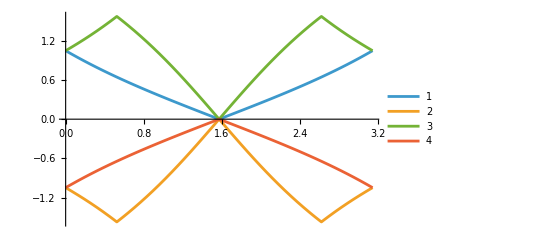

```mathematica
Plot[{ρs[[1]]/.{n->12},ρs[[2]]/.{n->12},ρs[[3]]/.{n->12},ρs[[4]]/.{n->12}},{θ,0,π},PlotLegends->Automatic]
```

# Origami constructor

θv                        -   The polar angle (i.e. angle with respect to the polar axis) of the ' main' crease. Range is from 0 to π (0 is “popped-up” and π is “popped-down”).
 rawSolnIdxs    -    Vector of folding branch IDs. There are two folding branches for each flap so this can take values 1 or 2. The length of this vector determines the number of folds.
                                    Specifically, the number of folds is twice the length of this vector.

```mathematica
ASymmWaterbomb[θv_,rawSolnIdxs_]:=Module[{origami,α,E1,e1,r,refTriA,nvec,ret,i,nl,refTri,QFlap,eaxis,tri,ρv,solnIdxs},
solnIdxs=rawSolnIdxs+Table[If[θv≥π/2,2,0],{i,1,Length[rawSolnIdxs]}]; (* Shift indices if we are below the flat state *)
nl=2*Length[solnIdxs];
α=2*π/nl;
E1={1,0,0};
r={Cos[α],Sin[α],0};
refTriA={{0,0,0},E1,r};
e1=Q[{0,1,0},π/2-θv].E1;
ret={};
For[i=1,i≤Length[solnIdxs],i++,
ρv=(ρs[[solnIdxs[[i]]]])/.{θ->θv,n->nl};
QFlap=Q[{0,0,1},2*(i-1)*α];
eaxis=QFlap.e1;
refTri=rotatePts[rotatePts[refTriA,Q[{0,1,0},π/2-θv]],QFlap];
tri=rotatePts[refTri,Q[eaxis,ρv]];
ret=Append[ret,Triangle[tri]];
nvec=(tri[[3]]×{0,0,1});
nvec=nvec/Sqrt[nvec.nvec];
ret=Append[ret,Triangle[reflPts[tri,{0,0,0},nvec]]];
];
ret
];
```

## Examples

```mathematica
Manipulate[Graphics3D[ASymmWaterbomb[θ,{1,1,1,1}],Boxed->False],{θ,0,3*π/4,π/32}]
```

```mathematica
Export["symm-folding.gif",%]
```

symm-folding.gif

```mathematica
Graphics3D[ASymmWaterbomb[7*π/12,{1,1,2}],Boxed->False]
```

-Graphics3D-

```mathematica
Manipulate[Graphics3D[ASymmWaterbomb[θv,{si1,si2,si3,si4,si5,si6}],Boxed->False],{{θv,π/4},0,π,π/16},{{si1,1},{1,2}},{{si2,1},{1,2}},{{si3,1},{1,2}},{{si4,1},{1,2}},{{si5,1},{1,2}},{{si6,1},{1,2}}]
```

```mathematica
Manipulate[Graphics3D[ASymmWaterbomb[θv,{si1,si2,si3,si4,si5,si6,si7}],Boxed->False],{{θv,π/4},0,π,π/16},{{si1,1},{1,2}},{{si2,1},{1,2}},{{si3,1},{1,2}},{{si4,1},{1,2}},{{si5,1},{1,2}},{{si6,1},{1,2}},{{si7,1},{1,2}}]
```

Note: Facet contact occurs on branch 1 at θ = 0 and π - (2π)/n      where n is the number of folds.
            Facet contact occurs on branch 2 at θ = (2π)/n and π

Note: a full cyclic permutation of the solution indices gives the same folding, just rigidly rotated. While technically you have 2^N choices for solution indices, many of them are the same in the sense that they are simply related through a rigid rotation (i.e. cyclic permutations of each other).

Note: reflecting θ about π/2 (i.e. θ -> π - θ) and changing the switch on all the solution indexes also gives the same structure (but reflected about the plane of the flat state)

```mathematica
Manipulate[Graphics3D[ASymmWaterbomb[θv,{si1,si2,si3,si4}],Boxed->False],{{θv,π/4},0,π,π/16},{{si1,1},{1,2}},{{si2,1},{1,2}},{{si3,1},{1,2}},{{si4,1},{1,2}}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

## Example export to STL

```mathematica
(*Export["test.stl", Graphics3D[ASymmWaterbomb[7*π/12,{1,1,2,2}],Boxed->False]]*)
```

```mathematica
Do[
Print[θ],
{θ,0,π,π/4}
]
```

0

π/4

π/2

(3 π)/4

π

## Finding Stable States

```mathematica
MatrixProduct[As_]:=Module[{ret,i},
ret=IdentityMatrix[Length[As[[1]]]];
For[i=1,i≤Length[As],i++,
ret=ret.As[[i]];
];
ret
];
```

```mathematica
bsSymm[n_]:=Table[{Cos[j*2*π/n],Sin[j*2*π/n],0},{j,0,n-1}];
foldMap[bs_,ϕs_,j_]:=If[j==1,IdentityMatrix[3],MatrixProduct[Table[Q[bs[[i]],ϕs[[i]]],{i,1,j-1}]]];
vertexLoopMap[bs_,ϕs_]:=foldMap[bs,ϕs,Length[bs]+1];
ϕsSymm[ρIdxs_]:=Module[{ret},
ret={ρs[[ρIdxs[[1]]]]+ρs[[ρIdxs[[Length[ρIdxs]]]]],If[Mod[ρIdxs[[1]],2]==1,-Abs[2*θ-π],Abs[2*θ-π]]};
For[i=2,i≤Length[ρIdxs],i++,
AppendTo[ret,ρs[[ρIdxs[[i]]]]+ρs[[ρIdxs[[i-1]]]]];
AppendTo[ret,If[Mod[ρIdxs[[i]],2]==1,-Abs[2*θ-π],Abs[2*θ-π]]];
];
ret
];
ϕsSymmN[ρIdxs_,θv_]:=N[(ϕsSymm[ρIdxs+If[θv<π/2,Table[0,{Length[ρIdxs]}],Table[2,{Length[ρIdxs]}]]])/.{θ->θv,n->2*Length[ρIdxs]}];
CMatrix[bs_,ϕs_]:=Transpose[Table[foldMap[bs,ϕs,j].bs[[j]],{j,1,Length[bs]}]];
```

```mathematica
Manipulate[MatrixForm[Transpose[foldMap[bsSymm[8],ϕsSymmN[{1,1,1,1},θv],idx]].foldMap[bsSymm[8],ϕsSymmN[{1,1,1,1},θv],idx]],{idx,1,9,1},{{θv,π/4},0,3*π/4,π/12}]
```

```mathematica
Manipulate[MatrixForm[vertexLoopMap[bsSymm[8],ϕsSymmN[{1,1,1,1},θv]]],{θv,0,3*π/4,π/12}]
```

```mathematica
Manipulate[
csLocal=Transpose[CMatrix[bsSymm[8],ϕsSymmN[{1,1,1,1},θv]]];
For[z=1,z≤Length[csLocal],z++,
Assert[csLocal[[z]].csLocal[[z]]-1<10^(-3)];
];
{MatrixForm[CMatrix[bsSymm[8],ϕsSymmN[{2,1,2,1},θv]]],MatrixForm[Table[csLocal[[j]].csLocal[[j]],{j,1,Length[csLocal]}]]},
{θv,0,3*π/4,π/12}
]
```

```mathematica
UExpr[ϕs_,rk_,ϕ0E_,ϕ0O_]:=Sum[1/2*(ϕs[[i]]-ϕ0O)^2,{i,1,Length[ϕs],2}]+Sum[rk/2*(ϕs[[i]]-ϕ0E)^2,{i,2,Length[ϕs],2}];
```

```mathematica
ϕ0sSymm[θ0_]:={2*(ρs[[If[θ0≤π/2,1,3]]])/.{θ->θ0},-Abs[2*θ0-π]};
```

```mathematica
UExprAsymm[ρIdxs_,rv_,θ0_]:=Module[{ϕ0s,ϕ0even,ϕ0odd,UExprL},
ϕ0s=ϕ0sSymm[θ0];
ϕ0odd=ϕ0s[[1]];
ϕ0even=ϕ0s[[2]];
UExprL=UExpr[ϕsSymm[ρIdxs],rv,ϕ0even,ϕ0odd]
]
```

```mathematica
dUAsymmExpr[ρIdxs_,rv_,θ0_]:=D[UExprAsymm[ρIdxs,rv,θ0],θ]/.{Abs'[Sin[(2 π)/n]+Sin[θ]]->Sign[Sin[(2 π)/n]+Sin[θ]],Abs'[Sin[(2 π)/n]-Sin[θ]]->Sign[Sin[(2 π)/n]-Sin[θ]],Abs'[-π+2 θ]->Sign[2*θ-π]}/.{n->2*Length[ρIdxs]};
```

The next two functions are probably the most important. Here is a description of the parameters
	cases		a matrix of which describes the way each flap is folded; each row is a “folding branch” of the entire origami (i.e. specifies how the origami is folding); the columns should be 1 or 2 and signify 						how each flap is being folded for that particular folding branch of the origami
	weights		vector of the number of configurations each branch corresponds to; length of `weights` should be equal to the number of rows of `cases`
	rk			crease stiffness ratio
	θ0			polar angle of the stress free configuration
	η			stable state tolerance (the energy well of the stable state must be this deep to be counted)
	
Here is a description of the output:
	numStabs		number of stable states
	stabFlags			1 if there is a stable state on that folding branch, 0 if there isn’t
	θStabs			polar angle of each stable state
	UStabs			energy of each stable state
	δs				normalized depth of energy well
	
Note: there are twice as many “branches” in the output as in the input. That is because the output differentiates between pushing the vertex up versus pushing the vertex down. Thus, the first half of the output flags correspond to pushing each folding branch up and the second half to pushing each folding branch down. So if Length[cases] = N, then stableFlags[[k]] where k < N tells you whether or not there is a stable configuration on folding branch k when pushing the vertex up and stabFlags[[N+k]] tells you whether or not there is a stable configuration on folding branch k when pushing the vertex down.

```mathematica
StabCount[cases_,weights_,rk_,θ0_,η_]:=Module[{j,k,count,flags,θStars,UStars,ηTests,casejk,igs,lbs,ubs,nL,dUL,rootL,UFlat,UStar,ηTestjk},
igs={7*π/16,9*π/16};
lbs={0,π/2};
ubs={π/2,π};
count=0;
flags={};
θStars={};
UStars={};
ηTests={};
nL=2*Length[cases[[1]]];
UFlat=N[UExprAsymm[cases[[1]],rk,θ0]/.{θ->π/2,n->nL}];
If[θ0≠π/2,
For[k=0,k≤1,k++,
For[j=1,j≤Length[cases],j++,
casejk=cases[[j]]+Table[2*k,{Length[cases[[j]]]}];
dUL=dUAsymmExpr[casejk,rk,θ0];
Quiet[rootL=FindRoot[dUL==0,{θ,igs[[k+1]],lbs[[k+1]],ubs[[k+1]]}]];
(*rootL=FindRoot[dUL==0,{θ,lbs[[k+1]],ubs[[k+1]]},Method->"Brent"];*)
UStar=N[UExprAsymm[casejk,rk,θ0]/.Catenate[{rootL,{n->nL}}]];
ηTestjk=(UFlat-UStar)/UFlat;
count+=If[ηTestjk≥η,weights[[j]],0];
flags=Append[flags,If[ηTestjk≥η,1,0]];
θStars=Append[θStars,θ/.rootL];
UStars=Append[UStars,UStar];
ηTests=Append[ηTests,ηTestjk];
];
];
<|numStabs->count,stabFlags->flags,θStabs->θStars,UStabs->UStars,δs->ηTests|>,
<|numStabs->1,stabFlags->Table[0,{2*Length[cases]}],θStabs->Table[N[π/2],{2*Length[cases]}],UStabs->Table[UFlat,{2*Length[cases]}],δs->Table[0,{2*Length[cases]}]|>
]
]
```

This function is the same except the output is formatted such that it can be more easily written to a delimited file

```mathematica
StabCountFlat[cases_,weights_,rk_,θ0_,η_]:=Module[{results},
results=StabCount[cases,weights,rk,θ0,η];
Catenate[{{results[numStabs]},results[stabFlags],results[θStabs],results[UStabs],results[δs]}]
];
```

Here some variables are defined which should make life easier:

```mathematica
SixFoldCases={{1,1,2},{1,2,2},{1,1,1},{2,2,2}};
SixFoldWeights={3,3,1,1};
```

```mathematica
EightFoldCases={{1,1,1,2},{2,2,2,1},{1,1,2,2},{1,2,1,2},{1,1,1,1},{2,2,2,2}};
EightFoldWeights={4,4,4,2,1,1};
```

```mathematica
TenFoldCases={{1,1,1,1,2},{2,2,2,2,1},{1,1,1,2,2},{1,1,1,2,2},{1,2,1,2,1},{2,1,2,1,2},{1,1,1,1,1},{2,2,2,2,2}};
TenFoldWeights={5,5,5,5,5,5,1,1};
```

```mathematica
TwelveFoldCases={{1,1,1,1,1,2},{2,2,2,2,2,1},{1,1,1,2,2,2},{1,1,1,1,2,2},{1,1,2,2,2,2},
{1,1,1,2,1,2},{2,2,2,1,2,1},{1,1,2,1,2,1},{2,2,1,2,1,2},
{1,1,2,1,1,2},{2,2,1,2,2,1},{1,2,1,2,1,2},{1,1,1,1,1,1},{2,2,2,2,2,2}
};
TwelveFoldWeights={6,6,6,6,6,6,6,6,6,3,3,2,1,1};
```

Example where I generate some STLs for a given parameter set

```mathematica
ExampleEightFoldStabCount=StabCount[
EightFoldCases,
EightFoldWeights,
10^(2), (* Stiffness ratio *)
5*π/8, (* Polar angle of stress free configuration *)
0.01          (* Empirically speaking, this value of δ seems to work well *)
]
```

<|numStabs→10,stabFlags→{1,0,0,0,1,0,1,0,0,0,1,0},θStabs→{1.37788,1.37445,1.37445,1.37445,1.17497,1.37445,1.77513,1.76715,1.57957,1.57966,1.9635,1.76715},UStabs→{99.903,228.056,163.984,163.684,4.26684,292.429,95.1845,221.691,129.721,129.72,1.74437×10^-28,285.218},δs→{0.230236,-0.757201,-0.263519,-0.261201,0.967124,-1.2532,0.266592,-0.708151,0.000484466,0.000489261,1.,-1.19764}|>

```mathematica
ExampleEightFoldStabCount[stabFlags]
```

{1,0,0,0,1,0,1,0,0,0,1,0}

```mathematica
RootFileName="D4_rk-00001000_theta0-5piDiv8_";
nB=Length[EightFoldCases];
For[k=0,k≤1,k++,
For[i=1,i≤nB,i++,
If[ExampleEightFoldStabCount[stabFlags][[i+k*nB]]==1,
Print[ToString[i+k*nB]<>": True"];
(*Export[RootFileName<>ToString[i+k*nB]<>".stl",Graphics3D[ASymmWaterbomb[ExampleEightFoldStabCount[θStabs][[i+k*nB]],EightFoldCases[[i]]],Boxed->False]]*)
,
Print[ToString[i+k*nB]<>": False"]
];
];
]
```

1: True

2: False

3: False

4: False

5: True

6: False

7: True

8: False

9: False

10: False

11: True

12: False

If you really wanted to get crazy, you could probably wrap the above example in a loop. I think a more targeted approach would be to look at the phase diagrams, pick out different parameter sets that look interesting, and generate stable states for that parameter set.

Below is an example of how I usually create a comma delimited file of stable states. These CSV files were what I used to make the modern art phase diagrams
The example file is formatted as follows:
	θ0, r, NStable, IsBranch1Stable, IsBranch2Stable, ..., θStab1, θStab2, ..., UStab1, UStab2, ..., δ1, δ2, ...
	
	where
	θ0 				is the polar angle of the stress free configuration
	r 				is the crease stiffness ratio
	NStable			is the total  number of stable states
	IsBranch1Stable	is 0 if the branch does not have a stable state, 1 if it does
	...
	θStab1			is the polar angle of the stable state on branch 1 (if it exists)
	...
	UStab1			is the energy of the stable state on branch 1 (if it exists)

I left this commented out because it is monstrously slow; if you want to create a database of stable states like this, expect it to take at least 2 min to several hours

```mathematica
(*
η=0.01;
Clear[q];
tps=N[Flatten[Table[{θ0,ν},{θ0,0,3*π/4,π/128},{ν,-2,2,0.05}]]];
Export["D4_degeneracy.csv",Table[Catenate[{
{tps[[q]],10^(tps[[q+1]])},
StabCountFlat[
EightFoldCases,
EightFoldWeights,
10^(tps[[q+1]]),
tps[[q]],
η
],
{η}
}],
{q,1,Length[tps],2}
]
]

For[k=1,k≤Length[tps],k=k+2,
result = StabCountFlat[
EightFoldCases,
EightFoldWeights,
10^(tps[[q+1]]),
tps[[q]],
η
];
nB=Length[EightFoldCases];
For[k=0,k≤1,k++,
For[i=1,i≤nB,i++,
If[result[stabFlags][[i+k*nB]]==1,
Print[ToString[i+k*nB]<>": True"];
Export[RootFileName<>ToString[i+k*nB]<>".stl",Graphics3D[ASymmWaterbomb[result[θStabs][[i+k*nB]],EightFoldCases[[i]]],Boxed->False]]
,
Print[ToString[i+k*nB]<>": False"]
];
];
]
];
*)
```

```mathematica
(*η=0.01;
tps=N[Flatten[Table[{θ0,ν},{θ0,0,3*π/4,π/4},{ν,-2,2,0.5}]]];
For[q=1,q≤Length[tps],q=q+2,
result = StabCount[
EightFoldCases,
EightFoldWeights,
10^(tps[[q+1]]),
tps[[q]],
η
];
nB=Length[EightFoldCases];
For[k=0,k≤1,k++,
For[i=1,i≤nB,i++,
If[result[stabFlags][[i+k*nB]]==1,
Print[ToString[i+k*nB]<>": True"];
Export[RootFileName<>ToString[q]<>"_"<>ToString[i+k*nB]<>".stl",Graphics3D[ASymmWaterbomb[result[θStabs][[i+k*nB]],EightFoldCases[[i]]],Boxed->False]]
,
Print[ToString[i+k*nB]<>": False"]
];
];
]
];*)
```

```mathematica
η=0.01;
Clear[q];
tps=N[Flatten[Table[{θ0,ν},{θ0,0,3*π/4,π/128},{ν,-2,2,0.05}]]];
Export["D4_degeneracy.csv",Table[Catenate[{
{tps[[q]],10^(tps[[q+1]])},
StabCountFlat[
EightFoldCases,
EightFoldWeights,
10^(tps[[q+1]]),
tps[[q]],
η
],
{η}
}],
{q,1,Length[tps],2}
]
]
```

D4_degeneracy.csv

# Unconstrained minimization

```mathematica
ρs
```

{ArcCos[Abs[Sin[(2 π)/n]+Sin[θ]]/(1+Sin[(2 π)/n] Sin[θ])],-ArcCos[Abs[Sin[(2 π)/n]-Sin[θ]]/(1-Sin[(2 π)/n] Sin[θ])],ArcCos[Abs[Sin[(2 π)/n]-Sin[θ]]/(1-Sin[(2 π)/n] Sin[θ])],-ArcCos[Abs[Sin[(2 π)/n]+Sin[θ]]/(1+Sin[(2 π)/n] Sin[θ])]}

```mathematica
MatrixForm[CMatrix[bsSymm[8],ϕsSymmN[{1,1,2,1},π/3]]]
```

(1 | 0.707107 | 0.25 | -0.487832 | -0.5 | 0.204989 | 0.25 | 0.707107
0 | 0.639109 | 0.939898 | 0.790387 | 0.189898 | -0.0778539 | -0.75 | -0.707107
0 | 0.302555 | -0.232577 | -0.370553 | -0.844949 | -0.975663 | -0.612372 | -1.11022×10^-16)

```mathematica
OrigamiVertex[bs_,ϕs_,Q_:IdentityMatrix[3]]:=Module[{cs},
cs=Transpose[CMatrix[bs,ϕs]];
Catenate[{{Triangle[
rotatePts[{{0,0,0},cs[[Length[cs]]],cs[[1]]},Q]
]},Table[Triangle[rotatePts[{{0,0,0},cs[[i]],cs[[i-1]]},Q]],{i,2,Length[cs]}]}]
];
```

```mathematica
Manipulate[Graphics3D[{
OrigamiVertex[bsSymm[8],ϕsSymmN[{1,1,1,1},θ]],
{
Red, Opacity[0.75],
Table[Arrow[{
(foldMap[bsSymm[8],ϕsSymmN[{1,1,1,1},θ],j+1].{0.75*Cos[j*2*π/8-π/8],0.75*Sin[j*2*π/8-π/8],0}),
(foldMap[bsSymm[8],ϕsSymmN[{1,1,1,1},θ],j+1].{0.75*Cos[j*2*π/8-π/8],0.75*Sin[j*2*π/8-π/8],0.35})
}],{j,1,8}]
}
},Boxed->False],{θ,0,3*π/4}]
```

```mathematica
Graphics3D[{Gray, Opacity[0.25],OrigamiVertex[bsSymm[8],ϕsSymmN[{1,1,1,1},π/2]]},Boxed->False]
```

-Graphics3D-

```mathematica
Manipulate[Graphics3D[{
OrigamiVertex[bsSymm[8],ϕsSymmN[{1,1,1,1},θ]],
{
Red, Opacity[0.75],
Table[Arrow[{
(foldMap[bsSymm[8],ϕsSymmN[{1,1,1,1},θ],j+1].{0.75*Cos[j*2*π/8-π/8],0.75*Sin[j*2*π/8-π/8],0}),
(foldMap[bsSymm[8],ϕsSymmN[{1,1,1,1},θ],j+1].{0.75*Cos[j*2*π/8-π/8],0.75*Sin[j*2*π/8-π/8],0.35})
}],{j,8,8}]
}
},Boxed->False],{θ,π/3,2*π/3,π/64}]
```

```mathematica
ϕ0sSymmN[θ0_,nv_]:=N[(Flatten[Table[ϕ0sSymm[θ0],{Floor[nv/2]}]])/.{n->nv}];
```

```mathematica
ϕ0sSymmN[2*π/3,8]
```

{2.29673,-1.0472,2.29673,-1.0472,2.29673,-1.0472,2.29673,-1.0472}

```mathematica
rToks[r_,nv_]:=N[Flatten[Table[{1,r},{Floor[nv/2]}]]];
```

```mathematica
gradU[ks_,ϕ0s_,ϕs_]:=N[Table[ks[[i]]*(ϕs[[i]]-ϕ0s[[i]]),{i,1,Length[ϕs]}]];
```

```mathematica
ProjectColSpace[A_]:=A.Inverse[Transpose[A].A].Transpose[A];
```

```mathematica
infFold[NCy_,gradUy_]:=-(ProjectColSpace[NCy]).gradUy;
```

```mathematica
admisSpace[bs_,ϕs_]:=Module[{unSpace,j},
unSpace=NullSpace[CMatrix[bs,ϕs]];
Transpose[Table[Normalize[unSpace[[j]]],{j,1,Length[unSpace]}]]
];
```

```mathematica
EulerFoldStep[bs_,ks_,ϕ0s_,ϕs_,ϵ_]:=ϕs+ϵ*infFold[admisSpace[bs,ϕs],gradU[ks,ϕ0s,ϕs]];
```

```mathematica
RK4FoldStep[bs_,ks_,ϕ0s_,ϕs_,ϵ_]:=Module[{K1,K2,K3,K4},
K1=infFold[admisSpace[bs,ϕs],gradU[ks,ϕ0s,ϕs]];
K2=infFold[admisSpace[bs,ϕs+K1*ϵ/2],gradU[ks,ϕ0s,ϕs+K1*ϵ/2]];
K3=infFold[admisSpace[bs,ϕs+K2*ϵ/2],gradU[ks,ϕ0s,ϕs+K2*ϵ/2]];
K4=infFold[admisSpace[bs,ϕs+ϵ*K3],gradU[ks,ϕ0s,ϕs+ϵ*K3]];
ϕs+ϵ/6*(K1+2*K2+2*K3+K4)
];
```

```mathematica
RVertexLoopMap[bs_,ϕs_]:=Norm[vertexLoopMap[bs,ϕs]-IdentityMatrix[3]];
```

```mathematica
ExampleEightFoldStabCount2=StabCount[
EightFoldCases,
EightFoldWeights,
1, (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01          (* Empirically speaking, this value of δ seems to work well *)
]
```

<|numStabs→16,stabFlags→{1,0,0,0,1,0,1,0,1,1,1,0},θStabs→{1.44354,1.37445,1.37445,1.37445,1.0472,1.37445,1.71722,1.76715,1.64433,1.68066,1.72857,1.76715},UStabs→{2.38555,5.90202,4.17191,3.87113,2.32344×10^-30,7.93292,1.84165,3.69368,2.45421,2.38992,1.26552,4.87923},δs→{0.0768818,-1.28386,-0.614375,-0.497984,1.,-2.06974,0.287349,-0.429317,0.0503106,0.0751911,0.510289,-0.888082}|>

```mathematica
ExampleEightFoldStabCount2[θStabs][[11]]
```

1.72857

```mathematica
Length[ExampleEightFoldStabCount2[θStabs]]
```

12

```mathematica
Manipulate[
bsLocal=bsSymm[8];
ϕsLocal=ϕsSymmN[{1,1,1,1},θv];
SCLocal=StabCount[
EightFoldCases,
EightFoldWeights,
rv, (* Stiffness ratio *)
θ0v, (* Polar angle of stress free configuration *)
0.01          (* Empirically speaking, this value of δ seems to work well *)
];
ϕsNewLocal=EulerFoldStep[bsLocal,rToks[rv,8],ϕ0sSymmN[θ0v,8],ϕsLocal,ϵv];
ϕsNewRK=RK4FoldStep[bsLocal,rToks[rv,8],ϕ0sSymmN[θ0v,8],ϕsLocal,ϵv];
{"ϕs=",MatrixForm[ϕsLocal],"aspace=",MatrixForm[admisSpace[bsLocal,ϕsLocal]],"gradUProj=",MatrixForm[infFold[admisSpace[bsLocal,ϕsLocal],gradU[rToks[rv,8],ϕ0sSymmN[θ0v,8],ϕsLocal]]],"gradU=",MatrixForm[gradU[rToks[rv,8],ϕ0sSymmN[θ0v,8],ϕsLocal]],"θStabs=",MatrixForm[SCLocal[θStabs]],"θStar=",SCLocal[θStabs][[11]],"ϕsEuler=",MatrixForm[ϕsNewLocal],"RNormEuler=",RVertexLoopMap[bsLocal,ϕsNewLocal],"ϕsRK4=",MatrixForm[ϕsNewRK],"RNormRK4=",RVertexLoopMap[bsLocal,ϕsNewRK]},
{{θv,π/4},0,3*π/4,π/12},{{θ0v,π/4},0,3*π/4,π/12},{{rv,1},0,100,1},{{ϵv,0.01},0.0,1.0,0.005}
]
```

```mathematica
Clear[OrigamiMin];
OrigamiMin[bs_,ks_,ϕ0s_,ϕsInit_,ϵ_,maxSteps_,gradUTol_,snapshotFreq_,foldStepper_:EulerFoldStep,regTol_:0,regMethod_:Automatic,regMaxIteractions_:100,updateFreq_:30]:=Module[{step,ϕss,ϕs,loopMapResidualNorms,origamis,admisSpaces,gradUProjs,aSpace,RNorm,mins,cs,gradUProj,resLocal,regFlags,start,lastUpdate,now},
ϕs=ϕsInit;
ϕss={};
loopMapResidualNorms={};
origamis={};
admisSpaces={};
regFlags={};
gradUProjs={};
start=AbsoluteTime[];
lastUpdate=start;
For[step=1,step≤maxSteps,step++,
ϕs=foldStepper[bs,ks,ϕ0s,ϕs,ϵ];
aSpace=admisSpace[bs,ϕs];
RNorm=RVertexLoopMap[bs,ϕs];
If[regTol≠0&&RNorm>regTol,
(*roots=FindRoot[vertexLoopMap[αs,Array[ϕ,Length[ϕs]]]==IdentityMatrix[3],Table[{ϕ[i],ϕs[[i]]},{i,1,Length[ϕs]}]];*)
mins=FindMinimum[
resLocal=vertexLoopMap[bs,Array[ϕ,Length[ϕs]]]-IdentityMatrix[3];
Tr[Transpose[resLocal].resLocal],
Table[{ϕ[i],ϕs[[i]]},{i,1,Length[ϕs]}],
Method->regMethod,
MaxIterations->regMaxIteractions
];
ϕs=If[mins[[1]]≤RNorm,(Array[ϕ,Length[ϕs]])/.mins[[2]],ϕs];
AppendTo[regFlags,mins[[1]]≤RNorm]
];
gradUProj=-infFold[aSpace,gradU[ks,ϕ0s,ϕs]];
If[Mod[step,snapshotFreq]==0||Norm[gradUProj]≤gradUTol,
AppendTo[ϕss,ϕs];
AppendTo[loopMapResidualNorms,RNorm];
AppendTo[admisSpaces,aSpace];
cs=Transpose[CMatrix[bs,ϕs]];
AppendTo[origamis,Graphics3D[Catenate[{OrigamiVertex[bs,ϕs],{Red,Thick,Table[Arrow[{{0,0,0},cs[[i]]}],{i,1,Length[cs]}]}}],Boxed->False]];
AppendTo[gradUProjs,gradUProj]
];
If[Norm[gradUProj]≤gradUTol,Break[]];
now=AbsoluteTime[];
If[now-lastUpdate≥updateFreq,
Print["Time elasped: ", now-start, ", Completed: ", step, "/", maxSteps, ", |ProjgradU|: ",Norm[gradUProj]];
lastUpdate=now
]
];
<|foldAngleSnapShots->ϕss,compatResidualNorms->loopMapResidualNorms,origamiGraphics->origamis,adSpaces->admisSpaces,gradUProjects->gradUProjs,regSuccesses->regFlags,numSteps->step|>
]
```

```mathematica
ϕsInit=ϕsSymmN[{1,1,1,1},11*π/24]
```

{0.108569,-0.261799,0.108569,-0.261799,0.108569,-0.261799,0.108569,-0.261799}

```mathematica
(*OrigamiMin[bs_,ks_,ϕ0s_,ϕs_,ϵ_,maxSteps_,gradUTol_,snapshotFreq_,foldStepper:EulerFoldStep,regTol_:0,regMethod_:Automatic,regMaxIteractions_:100,updateFreq_:30]*)
```

```mathematica
Timing[result01=OrigamiMin[bsSymm[8],rToks[1,8],ϕ0sSymmN[π/6,8],ϕsInit,10^(-2),10000,10^(-7),100,RK4FoldStep];]
```

{13.1563,Null}

```mathematica
Manipulate[{result01[origamiGraphics][[j]],result01[compatResidualNorms][[j]],MatrixForm[result01[adSpaces][[j]]],MatrixForm[result01[gradUProjects][[j]]]},{j,1,Length[result01[origamiGraphics]],1}]
```

```mathematica
Timing[result02=OrigamiMin[bsSymm[8],rToks[1,8],ϕ0sSymmN[π/6,8],ϕsSymmN[{1,1,1,1},13*π/24],10^(-2),10000,10^(-7),100,RK4FoldStep];]
```

{14.3906,Null}

```mathematica
Manipulate[{result02[origamiGraphics][[j]],result02[compatResidualNorms][[j]],MatrixForm[result02[adSpaces][[j]]],MatrixForm[result02[gradUProjects][[j]]]},{j,1,Length[result02[origamiGraphics]],1}]
```

```mathematica
EightFoldStabCount03=StabCount[
EightFoldCases,
EightFoldWeights,
1, (* Stiffness ratio *)
π/6, (* Polar angle of stress free configuration *)
0.01          (* Empirically speaking, this value of δ seems to work well *)
];
EightFoldStabCount03[stabFlags]
```

{1,0,0,0,1,0,1,0,1,1,1,0}

```mathematica
EightFoldStabCount03[θStabs][[1]]
```

1.30063

```mathematica
EightFoldCases
```

{{1,1,1,2},{2,2,2,1},{1,1,2,2},{1,2,1,2},{1,1,1,1},{2,2,2,2}}

```mathematica
Timing[result03=OrigamiMin[bsSymm[8],rToks[1,8],ϕ0sSymmN[π/6,8],ϕsSymmN[{1,2,1,2},15*π/24],10^(-2),10000,10^(-7),20,RK4FoldStep];]
```

{14.5938,Null}

```mathematica
Manipulate[{result03[origamiGraphics][[j]],result03[compatResidualNorms][[j]],MatrixForm[result03[adSpaces][[j]]],MatrixForm[result03[gradUProjects][[j]]]},{j,1,Length[result03[origamiGraphics]],1}]
```

```mathematica
Export["TestEnergyMin02.gif",%]
```

TestEnergyMin02.gif

```mathematica
Clear[StabCountUnconstrained];
StabCountUnconstrained[cases_,weights_,rk_,θ0_,η_,configTol_:10^(-2)]:=Module[{j,k,count,flags,ϕStars,UStars,ηTests,casejk,igs,lbs,ubs,nL,dUL,rootL,UFlat,UStar,ηTestjk,ucMinjk,minConfigs,minConfigjk,unique,m,ϕ0s,ks,origamis},
igs={7*π/16,9*π/16};
lbs={0,π/2};
ubs={π/2,π};
count=0;
flags={};
ϕStars={};
UStars={};
ηTests={};
minConfigs={};
origamis={};
nL=2*Length[cases[[1]]];
UFlat=N[UExprAsymm[cases[[1]],rk,θ0]/.{θ->π/2,n->nL}];
ϕ0s=ϕ0sSymmN[θ0,nL];
ks=rToks[rk,nL];
If[θ0≠π/2,
For[k=0,k≤1,k++,
For[j=1,j≤Length[cases],j++,
casejk=cases[[j]]+Table[2*k,{Length[cases[[j]]]}];
Print[casejk];
dUL=dUAsymmExpr[casejk,rk,θ0];
Quiet[rootL=FindRoot[dUL==0,{θ,igs[[k+1]],lbs[[k+1]],ubs[[k+1]]}]];
(*rootL=FindRoot[dUL==0,{θ,lbs[[k+1]],ubs[[k+1]]},Method->"Brent"];*)
Print["Unconstrained minimization..."];
Print[Timing[ucMinjk=OrigamiMin[bsSymm[nL],rToks[rk,nL],ϕ0sSymmN[θ0,nL],ϕsSymmN[cases[[j]],θ/.rootL],10^(-2),10000,10^(-7),10001,RK4FoldStep];]];
minConfigjk=Last[ucMinjk[foldAngleSnapShots]];
unique=True;
For[m=1,m≤Length[minConfigs],m++,
If[Norm[minConfigs[[m]]-minConfigjk]≤configTol,unique=False;Break[]]
];
UStar=Sum[ks[[m]]/2*(minConfigjk[[m]]-ϕ0s[[m]])^2,{m,1,Length[ks]}];
ηTestjk=(UFlat-UStar)/UFlat;
If[unique&&ηTestjk≥η,
AppendTo[minConfigs,minConfigjk]; 
AppendTo[origamis,Last[ucMinjk[origamiGraphics]]];
count+=weights[[j]]
];
AppendTo[flags,If[ηTestjk≥η,1,0]];
AppendTo[ϕStars,minConfigjk];
AppendTo[UStars,UStar];
AppendTo[ηTests,ηTestjk];
Print[];
];
];
<|numStabs->count,stabFlags->flags,ϕsStabs->ϕStars,UStabs->UStars,δs->ηTests,origamiGraphics->origamis|>,
<|numStabs->1,stabFlags->Table[0,{2*Length[cases]}],ϕsStabs->Table[N[π/2],{2*Length[cases]}],UStabs->Table[UFlat,{2*Length[cases]}],δs->Table[0,{2*Length[cases]}],origamiGraphics->{}|>
]
]
```

```mathematica
StabCountSix00=StabCountUnconstrained[
Reverse[SixFoldCases],
Reverse[SixFoldWeights],
1, (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01          (* Empirically speaking, this value of δ seems to work well *)
]
```

{2,2,2}

Unconstrained minimization...

{8.28125,Null}

{1,1,1}

Unconstrained minimization...

{0.015625,Null}

{1,2,2}

Unconstrained minimization...

{7.64063,Null}

{1,1,2}

Unconstrained minimization...

{8.03125,Null}

{4,4,4}

Unconstrained minimization...

{7.79688,Null}

{3,3,3}

Unconstrained minimization...

{0.,Null}

{3,4,4}

Unconstrained minimization...

{6.90625,Null}

{3,3,4}

Unconstrained minimization...

{7.35938,Null}

<|numStabs→2,stabFlags→{1,1,1,1,1,1,1,1},ϕsStabs→{{0.532853,-0.143566,0.532853,-0.143566,0.532853,-0.143566},{0.286695,-1.0472,0.286695,-1.0472,0.286695,-1.0472},{0.286695,-1.0472,0.286695,-1.0472,0.286695,-1.0472},{0.286695,-1.0472,0.286695,-1.0472,0.286695,-1.0472},{0.286695,-1.0472,0.286695,-1.0472,0.286695,-1.0472},{0.532853,-0.143566,0.532853,-0.143566,0.532853,-0.143566},{0.532853,-0.143566,0.532853,-0.143566,0.532853,-0.143566},{0.532853,-0.143566,0.532853,-0.143566,0.532853,-0.143566}},UStabs→{1.31571,7.39557×10^-32,4.95037×10^-15,4.93289×10^-15,4.97819×10^-15,1.31571,1.31571,1.31571},δs→{0.255913,1.,1.,1.,1.,0.255913,0.255913,0.255913},origamiGraphics→{-Graphics3D-,-Graphics3D-}|>

```mathematica
StabCountSix01=StabCountUnconstrained[
Reverse[SixFoldCases],
Reverse[SixFoldWeights],
0.1, (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01          (* Empirically speaking, this value of δ seems to work well *)
]
```

{2,2,2}

Unconstrained minimization...

{7.96875,Null}

{1,1,1}

Unconstrained minimization...

{0.,Null}

{1,2,2}

Unconstrained minimization...

Time elasped: 30.003549, Completed: 4663/10000, |ProjgradU|: 0.00014413

{40.1719,Null}

{1,1,2}

Unconstrained minimization...

Time elasped: 30.004988, Completed: 4676/10000, |ProjgradU|: 0.000111654

{39.7188,Null}

{4,4,4}

Unconstrained minimization...

Time elasped: 30.008123, Completed: 4669/10000, |ProjgradU|: 0.000182924

{40.2969,Null}

{3,3,3}

Unconstrained minimization...

{8.17188,Null}

{3,4,4}

Unconstrained minimization...

{7.90625,Null}

{3,3,4}

Unconstrained minimization...

{8.53125,Null}

<|numStabs→2,stabFlags→{1,1,1,1,1,1,1,1},ϕsStabs→{{0.312653,-0.0839337,0.312653,-0.0839337,0.312653,-0.0839337},{0.286695,-1.0472,0.286695,-1.0472,0.286695,-1.0472},{0.286695,-1.0472,0.286695,-1.0472,0.286695,-1.0472},{0.286695,-1.0472,0.286695,-1.0472,0.286695,-1.0472},{0.286695,-1.0472,0.286695,-1.0472,0.286695,-1.0472},{0.312653,-0.0839337,0.312653,-0.0839337,0.312653,-0.0839337},{0.312653,-0.0839338,0.312653,-0.0839337,0.312653,-0.0839337},{0.312653,-0.0839338,0.312653,-0.0839338,0.312653,-0.0839336}},UStabs→{0.140192,1.45619×10^-29,2.97086×10^-14,2.97037×10^-14,2.97037×10^-14,0.140192,0.140192,0.140192},δs→{0.512857,1.,1.,1.,1.,0.512857,0.512857,0.512857},origamiGraphics→{-Graphics3D-,-Graphics3D-}|>

```mathematica
StabCountSix02=StabCountUnconstrained[
Reverse[SixFoldCases],
Reverse[SixFoldWeights],
10.0, (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01          (* Empirically speaking, this value of δ seems to work well *)
]
```

{2,2,2}

Unconstrained minimization...

{1.4375,Null}

{1,1,1}

Unconstrained minimization...

{0.015625,Null}

{1,2,2}

Unconstrained minimization...

{1.9375,Null}

{1,1,2}

Unconstrained minimization...

{1.60938,Null}

{4,4,4}

Unconstrained minimization...

{0.828125,Null}

{3,3,3}

Unconstrained minimization...

{0.,Null}

{3,4,4}

Unconstrained minimization...

{4.57813,Null}

{3,3,4}

Unconstrained minimization...

{5.45313,Null}

<|numStabs→2,stabFlags→{1,1,1,1,1,1,1,1},ϕsStabs→{{0.2867,-1.0472,0.286708,-1.0472,0.286673,-1.0472},{0.286695,-1.0472,0.286695,-1.0472,0.286695,-1.0472},{0.286695,-1.0472,0.286695,-1.0472,0.286695,-1.0472},{0.286695,-1.0472,0.286695,-1.0472,0.286695,-1.0472},{0.286695,-1.0472,0.286695,-1.0472,0.286695,-1.0472},{1.9275,-0.556919,1.9275,-0.556919,1.9275,-0.556919},{1.9275,-0.556919,1.9275,-0.556919,1.9275,-0.556918},{1.9275,-0.556919,1.9275,-0.556919,1.9275,-0.556919}},UStabs→{3.85596×10^-10,7.39557×10^-31,4.10711×10^-15,3.0389×10^-15,8.41534×10^-15,7.64396,7.64395,7.64395},δs→{1.,1.,1.,1.,1.,0.53876,0.538761,0.53876},origamiGraphics→{-Graphics3D-,-Graphics3D-}|>

```mathematica
StabCountTen00=StabCountUnconstrained[
Reverse[TenFoldCases],
Reverse[TenFoldWeights],
1, (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01          (* Empirically speaking, this value of δ seems to work well *)
]
```

{2,2,2,2,2}

Unconstrained minimization...

Time elasped: 30.003139, Completed: 1513/10000, |ProjgradU|: 1.42628×10^-6

{24.6563,Null}

{1,1,1,1,1}

Unconstrained minimization...

{0.015625,Null}

{2,1,2,1,2}

Unconstrained minimization...

Time elasped: 30.015302, Completed: 1498/10000, |ProjgradU|: 1.10197×10^-6

{25.8438,Null}

{1,2,1,2,1}

Unconstrained minimization...

Time elasped: 30.016007, Completed: 1491/10000, |ProjgradU|: 9.85265×10^-7

{25.4063,Null}

{1,1,1,2,2}

Unconstrained minimization...

Time elasped: 30.003716, Completed: 1502/10000, |ProjgradU|: 9.07008×10^-7

{25.7813,Null}

{1,1,1,2,2}

Unconstrained minimization...

Time elasped: 30.015065, Completed: 1505/10000, |ProjgradU|: 8.80202×10^-7

{24.2813,Null}

{2,2,2,2,1}

Unconstrained minimization...

Time elasped: 30.015091, Completed: 1497/10000, |ProjgradU|: 1.3073×10^-6

{24.8906,Null}

{1,1,1,1,2}

Unconstrained minimization...

Time elasped: 30.025246, Completed: 1448/10000, |ProjgradU|: 1.2145×10^-6

{25.1563,Null}

{4,4,4,4,4}

Unconstrained minimization...

Time elasped: 30.015328, Completed: 1207/10000, |ProjgradU|: 0.0000207596

{30.3594,Null}

{3,3,3,3,3}

Unconstrained minimization...

{0.015625,Null}

{4,3,4,3,4}

Unconstrained minimization...

Time elasped: 30.018744, Completed: 1225/10000, |ProjgradU|: 0.0000126216

{28.5625,Null}

{3,4,3,4,3}

Unconstrained minimization...

Time elasped: 30.015799, Completed: 1238/10000, |ProjgradU|: 7.21609×10^-6

{27.5469,Null}

{3,3,3,4,4}

Unconstrained minimization...

Time elasped: 30.027119, Completed: 1230/10000, |ProjgradU|: 8.70644×10^-6

{28.3125,Null}

{3,3,3,4,4}

Unconstrained minimization...

Time elasped: 30.027137, Completed: 1241/10000, |ProjgradU|: 7.81652×10^-6

{30.0156,Null}

{4,4,4,4,3}

Unconstrained minimization...

Time elasped: 30.026432, Completed: 1208/10000, |ProjgradU|: 0.0000159614

{31.5,Null}

{3,3,3,3,4}

Unconstrained minimization...

Time elasped: 30.003326, Completed: 1238/10000, |ProjgradU|: 3.58112×10^-6

{28.6719,Null}

<|numStabs→2,stabFlags→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},ϕsStabs→{{0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758},{0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472},{0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472},{0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472},{0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472},{0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472},{0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472},{0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472},{0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472,0.542752,-1.0472},{0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758},{0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758},{0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758},{0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758},{0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758},{0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758},{0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758,0.860968,-0.443758}},UStabs→{1.1635,7.05661×10^-30,4.99689×10^-15,4.97746×10^-15,4.95006×10^-15,4.95006×10^-15,4.90638×10^-15,4.96926×10^-15,4.95613×10^-15,1.1635,1.1635,1.1635,1.1635,1.1635,1.1635,1.1635},δs→{0.665469,1.,1.,1.,1.,1.,1.,1.,1.,0.665469,0.665469,0.665469,0.665469,0.665469,0.665469,0.665469},origamiGraphics→{-Graphics3D-,-Graphics3D-}|>

```mathematica
StabCountTen01=StabCountUnconstrained[
Reverse[TenFoldCases],
Reverse[TenFoldWeights],
0.1, (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01          (* Empirically speaking, this value of δ seems to work well *)
]
```

{2,2,2,2,2}

Unconstrained minimization...

Time elasped: 30.002457, Completed: 1227/10000, |ProjgradU|: 0.000133246

{36.4375,Null}

{1,1,1,1,1}

Unconstrained minimization...

{0.,Null}

{2,1,2,1,2}

Unconstrained minimization...

Time elasped: 30.008509, Completed: 1274/10000, |ProjgradU|: 0.0189415

Time elasped: 60.0188658, Completed: 2762/10000, |ProjgradU|: 0.000825751

Time elasped: 90.0226963, Completed: 4266/10000, |ProjgradU|: 0.000177571

Time elasped: 120.026097, Completed: 5745/10000, |ProjgradU|: 0.0000404594

Time elasped: 150.02948, Completed: 7233/10000, |ProjgradU|: 9.1367×10^-6

Time elasped: 180.03312, Completed: 8731/10000, |ProjgradU|: 2.04276×10^-6

{131.234,Null}

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Part::partw: Part 3 of Last[{}] does not exist.

Part::partw: Part 4 of Last[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{1,2,1,2,1}

Unconstrained minimization...

Time elasped: 30.027313, Completed: 1477/10000, |ProjgradU|: 0.00957322

Time elasped: 60.031191, Completed: 2780/10000, |ProjgradU|: 0.00114169

Time elasped: 90.0347394, Completed: 3979/10000, |ProjgradU|: 0.000340628

$Aborted

```mathematica
StabCountTen02=StabCountUnconstrained[
Reverse[TenFoldCases],
Reverse[TenFoldWeights],
10, (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01          (* Empirically speaking, this value of δ seems to work well *)
]
```

{2,2,2,2,2}

Unconstrained minimization...

{14.3739,Null}

{1,1,1,1,1}

Unconstrained minimization...

{0.037318,Null}

{2,1,2,1,2}

Unconstrained minimization...

Time elasped: 30.00867, Completed: 1323/10000, |ProjgradU|: 6.4451×10^-7

{34.5286,Null}

{1,2,1,2,1}

Unconstrained minimization...

Time elasped: 30.01233, Completed: 1252/10000, |ProjgradU|: 4.8872×10^-7

{33.6779,Null}

{1,1,1,2,2}

Unconstrained minimization...

$Aborted

```mathematica
StabCount00=StabCountUnconstrained[
Reverse[EightFoldCases],
Reverse[EightFoldWeights],
0, (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01          (* Empirically speaking, this value of δ seems to work well *)
]
```

{2,2,2,2}

Unconstrained minimization...

Time elasped: 30.00965, Completed: 1523/10000, |ProjgradU|: 5.94327×10^-6

{39.2779,Null}

{1,1,1,1}

Unconstrained minimization...

{0.024376,Null}

{1,2,1,2}

Unconstrained minimization...

Time elasped: 30.0057, Completed: 1761/10000, |ProjgradU|: 0.0211534

Time elasped: 60.012994, Completed: 3599/10000, |ProjgradU|: 0.00110672

Time elasped: 90.018457, Completed: 5431/10000, |ProjgradU|: 0.0000576231

Time elasped: 120.01943, Completed: 7312/10000, |ProjgradU|: 2.77004×10^-6

Time elasped: 150.02796, Completed: 9241/10000, |ProjgradU|: 1.23231×10^-7

{152.22,Null}

{1,1,2,2}

Unconstrained minimization...

Time elasped: 30.00364, Completed: 1945/10000, |ProjgradU|: 0.0164455

Time elasped: 60.007971, Completed: 3866/10000, |ProjgradU|: 0.000750964

Time elasped: 90.009623, Completed: 5730/10000, |ProjgradU|: 0.0000371594

Time elasped: 120.01683, Completed: 7310/10000, |ProjgradU|: 2.90562×10^-6

Time elasped: 150.02114, Completed: 8918/10000, |ProjgradU|: 2.17162×10^-7

{155.55,Null}

{2,2,2,1}

Unconstrained minimization...

Time elasped: 30.00066, Completed: 1495/10000, |ProjgradU|: 0.0385607

Time elasped: 60.017778, Completed: 3017/10000, |ProjgradU|: 0.00340133

Time elasped: 90.024011, Completed: 4776/10000, |ProjgradU|: 0.000199755

Time elasped: 120.03291, Completed: 6271/10000, |ProjgradU|: 0.0000179168

Time elasped: 150.04562, Completed: 7875/10000, |ProjgradU|: 1.34775×10^-6

{175.418,Null}

{1,1,1,2}

Unconstrained minimization...

Time elasped: 30.00658, Completed: 1647/10000, |ProjgradU|: 0.0216277

Time elasped: 60.012345, Completed: 3512/10000, |ProjgradU|: 0.00108319

Time elasped: 90.018952, Completed: 5809/10000, |ProjgradU|: 0.00002662

Time elasped: 120.02558, Completed: 7573/10000, |ProjgradU|: 1.54496×10^-6

{147.593,Null}

{4,4,4,4}

Unconstrained minimization...

Time elasped: 30.00284, Completed: 1841/10000, |ProjgradU|: 7.88247×10^-7

{33.9153,Null}

{3,3,3,3}

Unconstrained minimization...

{0.023203,Null}

{3,4,3,4}

Unconstrained minimization...

{0.023028,Null}

{3,3,4,4}

Unconstrained minimization...

Time elasped: 30.01933, Completed: 2010/10000, |ProjgradU|: 0.0000206381

{41.6664,Null}

{4,4,4,3}

Unconstrained minimization...

$Aborted

```mathematica
StabCount01=StabCountUnconstrained[
Reverse[EightFoldCases],
Reverse[EightFoldWeights],
10^(-3), (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01          (* Empirically speaking, this value of δ seems to work well *)
]
```

{2,2,2,2}

Unconstrained minimization...

$Aborted

```mathematica
StabCount02=StabCountUnconstrained[
Reverse[EightFoldCases],
Reverse[EightFoldWeights],
10^(-2), (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01          (* Empirically speaking, this value of δ seems to work well *)
]
```

{2,2,2,2}

Unconstrained minimization...

{15.1277,Null}

{1,1,1,1}

Unconstrained minimization...

{0.013977,Null}

{1,2,1,2}

Unconstrained minimization...

Time elasped: 30.00225, Completed: 3862/10000, |ProjgradU|: 0.000564893

Time elasped: 60.008426, Completed: 7610/10000, |ProjgradU|: 0.0000898667

{79.0934,Null}

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Part::partw: Part 3 of Last[{}] does not exist.

Part::partw: Part 4 of Last[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{1,1,2,2}

Unconstrained minimization...

Time elasped: 30.00315, Completed: 3797/10000, |ProjgradU|: 0.000641016

Time elasped: 60.008642, Completed: 7592/10000, |ProjgradU|: 1.02403×10^-6

{70.9357,Null}

{2,2,2,1}

Unconstrained minimization...

Time elasped: 30.00747, Completed: 3782/10000, |ProjgradU|: 0.000759689

Time elasped: 60.010026, Completed: 7593/10000, |ProjgradU|: 7.77134×10^-6

{79.0783,Null}

Last::nolast: {} has zero length and no last element.

{1,1,1,2}

Unconstrained minimization...

Time elasped: 30.00701, Completed: 3800/10000, |ProjgradU|: 0.000539061

Time elasped: 60.010111, Completed: 7608/10000, |ProjgradU|: 0.000099675

{79.4494,Null}

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

{4,4,4,4}

Unconstrained minimization...

Time elasped: 30.00325, Completed: 3792/10000, |ProjgradU|: 0.000970872

Time elasped: 60.009157, Completed: 7789/10000, |ProjgradU|: 1.10114×10^-6

{70.6075,Null}

{3,3,3,3}

Unconstrained minimization...

{0.013661,Null}

{3,4,3,4}

Unconstrained minimization...

Time elasped: 30.00416, Completed: 4036/10000, |ProjgradU|: 0.0100971

Time elasped: 60.007773, Completed: 8068/10000, |ProjgradU|: 0.00377162

{74.4349,Null}

{3,3,4,4}

Unconstrained minimization...

{22.4504,Null}

{4,4,4,3}

Unconstrained minimization...

Time elasped: 30.00021, Completed: 4035/10000, |ProjgradU|: 0.00443594

Time elasped: 60.004584, Completed: 8071/10000, |ProjgradU|: 0.00144707

{74.4749,Null}

{3,3,3,4}

Unconstrained minimization...

Time elasped: 30.00215, Completed: 4038/10000, |ProjgradU|: 0.00231706

Time elasped: 60.007416, Completed: 8056/10000, |ProjgradU|: 0.000742312

{74.6122,Null}

<|numStabs→2,stabFlags→{1,1,If[{}≥0.01,1,0],1,If[{}≥0.01,1,0],If[{}≥0.01,1,0],1,1,If[{}≥0.01,1,0],1,If[{}≥0.01,1,0],If[{}≥0.01,1,0]},ϕsStabs→{{0.44575,-0.185271,0.44575,-0.185271,0.44575,-0.185271,0.44575,-0.185271},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},Last[{}],{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},Last[{}],Last[{}],{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.44575,-0.185271,0.44575,-0.185271,0.44575,-0.185271,0.44575,-0.185271},Last[{}],{0.44575,-0.185271,0.44575,-0.185271,0.44575,-0.185271,0.44575,-0.185271},Last[{}],Last[{}]},UStabs→{0.0148844,2.4467×10^-30,{},2.94579×10^-14,{},{},2.94362×10^-14,0.0148844,{},0.0148844,{},{}},δs→{0.963953,1.,{},1.,{},{},1.,0.963953,{},0.963953,{},{}},origamiGraphics→{-Graphics3D-,-Graphics3D-}|>

```mathematica
StabCount03=StabCountUnconstrained[
Reverse[EightFoldCases],
Reverse[EightFoldWeights],
10^(-1), (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01          (* Empirically speaking, this value of δ seems to work well *)
]
```

{2,2,2,2}

Unconstrained minimization...

{14.8194,Null}

{1,1,1,1}

Unconstrained minimization...

{0.020508,Null}

{1,2,1,2}

Unconstrained minimization...

Time elasped: 30.00574, Completed: 3986/10000, |ProjgradU|: 0.000162823

Time elasped: 60.008971, Completed: 8005/10000, |ProjgradU|: 2.87165×10^-6

{74.9682,Null}

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Part::partw: Part 3 of Last[{}] does not exist.

Part::partw: Part 4 of Last[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{1,1,2,2}

Unconstrained minimization...

Time elasped: 30.00606, Completed: 4002/10000, |ProjgradU|: 0.0000318861

{47.735,Null}

{2,2,2,1}

Unconstrained minimization...

Time elasped: 30.00398, Completed: 3983/10000, |ProjgradU|: 0.0000503067

Time elasped: 60.009683, Completed: 7966/10000, |ProjgradU|: 5.91414×10^-7

{73.396,Null}

{1,1,1,2}

Unconstrained minimization...

Time elasped: 30.00355, Completed: 3980/10000, |ProjgradU|: 0.000128832

Time elasped: 60.005332, Completed: 7955/10000, |ProjgradU|: 2.36635×10^-6

{76.5419,Null}

Last::nolast: {} has zero length and no last element.

{4,4,4,4}

Unconstrained minimization...

Time elasped: 30.00653, Completed: 3976/10000, |ProjgradU|: 0.0000485536

{49.0033,Null}

{3,3,3,3}

Unconstrained minimization...

{0.012857,Null}

{3,4,3,4}

Unconstrained minimization...

Time elasped: 30.00031, Completed: 3962/10000, |ProjgradU|: 7.40055×10^-6

{42.0748,Null}

{3,3,4,4}

Unconstrained minimization...

{18.4568,Null}

{4,4,4,3}

Unconstrained minimization...

Time elasped: 30.00399, Completed: 3981/10000, |ProjgradU|: 1.28826×10^-6

{37.2079,Null}

{3,3,3,4}

Unconstrained minimization...

Time elasped: 30.00166, Completed: 3987/10000, |ProjgradU|: 1.51956×10^-6

{37.6852,Null}

<|numStabs→2,stabFlags→{1,1,If[{}≥0.01,1,0],1,1,If[{}≥0.01,1,0],1,1,1,1,1,1},ϕsStabs→{{0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},Last[{}],{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},Last[{}],{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656},{0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656},{0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656},{0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656},{0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656}},UStabs→{0.146534,9.86076×10^-33,{},2.03241×10^-14,4.9934×10^-14,{},2.03753×10^-14,0.146534,0.146534,0.146534,0.146534,0.146534},δs→{0.7599,1.,{},1.,1.,{},1.,0.7599,0.7599,0.7599,0.7599,0.7599},origamiGraphics→{-Graphics3D-,-Graphics3D-}|>

```mathematica
StabCount04=StabCountUnconstrained[
Reverse[EightFoldCases],
Reverse[EightFoldWeights],
10^(0), (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01          (* Empirically speaking, this value of δ seems to work well *)
]
```

{2,2,2,2}

Unconstrained minimization...

{13.257,Null}

{1,1,1,1}

Unconstrained minimization...

{0.013544,Null}

{1,2,1,2}

Unconstrained minimization...

{12.8405,Null}

{1,1,2,2}

Unconstrained minimization...

{12.9655,Null}

{2,2,2,1}

Unconstrained minimization...

{13.2777,Null}

{1,1,1,2}

Unconstrained minimization...

{12.7769,Null}

{4,4,4,4}

Unconstrained minimization...

{12.9947,Null}

{3,3,3,3}

Unconstrained minimization...

{0.012848,Null}

{3,4,3,4}

Unconstrained minimization...

{12.4243,Null}

{3,3,4,4}

Unconstrained minimization...

{12.4977,Null}

{4,4,4,3}

Unconstrained minimization...

{12.5783,Null}

{3,3,3,4}

Unconstrained minimization...

{11.8624,Null}

<|numStabs→2,stabFlags→{1,1,1,1,1,1,1,1,1,1,1,1},ϕsStabs→{{0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539},{0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539},{0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539},{0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539},{0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539}},UStabs→{1.26552,2.32344×10^-30,4.90805×10^-15,4.99156×10^-15,4.92121×10^-15,4.9476×10^-15,4.9725×10^-15,1.26552,1.26552,1.26552,1.26552,1.26552},δs→{0.510289,1.,1.,1.,1.,1.,1.,0.510289,0.510289,0.510289,0.510289,0.510289},origamiGraphics→{-Graphics3D-,-Graphics3D-}|>

```mathematica
StabCount05=StabCountUnconstrained[
Reverse[EightFoldCases],
Reverse[EightFoldWeights],
10^(1), (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01          (* Empirically speaking, this value of δ seems to work well *)
]
```

{2,2,2,2}

Unconstrained minimization...

{5.64771,Null}

{1,1,1,1}

Unconstrained minimization...

{0.013496,Null}

{1,2,1,2}

Unconstrained minimization...

{1.73778,Null}

{1,1,2,2}

Unconstrained minimization...

{9.63158,Null}

{2,2,2,1}

Unconstrained minimization...

{2.78972,Null}

{1,1,1,2}

Unconstrained minimization...

{2.71751,Null}

{4,4,4,4}

Unconstrained minimization...

{1.71277,Null}

{3,3,3,3}

Unconstrained minimization...

{0.012851,Null}

{3,4,3,4}

Unconstrained minimization...

{5.76736,Null}

{3,3,4,4}

Unconstrained minimization...

{5.49024,Null}

{4,4,4,3}

Unconstrained minimization...

{5.53388,Null}

{3,3,3,4}

Unconstrained minimization...

{5.36994,Null}

<|numStabs→2,stabFlags→{1,1,1,1,1,1,1,1,1,1,1,1},ϕsStabs→{{1.77014,-0.775296,1.77014,-0.775297,1.77014,-0.775296,1.77014,-0.775295},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{1.77014,-0.775297,1.77014,-0.775297,1.77014,-0.775297,1.77014,-0.775297},{1.77013,-0.775296,1.77012,-0.775297,1.77013,-0.775296,1.77014,-0.775293},{1.77014,-0.775296,1.77013,-0.775297,1.77013,-0.775296,1.77014,-0.775294},{1.77014,-0.775297,1.77014,-0.775297,1.77014,-0.775297,1.77014,-0.775296},{1.77014,-0.775297,1.77014,-0.775297,1.77014,-0.775297,1.77014,-0.775296}},UStabs→{5.00575,9.86076×10^-31,2.95129×10^-15,1.03969×10^-14,1.6103×10^-14,1.82255×10^-15,6.83674×10^-15,5.00577,5.00572,5.00575,5.00576,5.00577},δs→{0.775763,1.,1.,1.,1.,1.,1.,0.775762,0.775764,0.775763,0.775762,0.775762},origamiGraphics→{-Graphics3D-,-Graphics3D-}|>

```mathematica
StabCount06=StabCountUnconstrained[
Reverse[EightFoldCases],
Reverse[EightFoldWeights],
10^(2), (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01          (* Empirically speaking, this value of δ seems to work well *)
]
```

{2,2,2,2}

Unconstrained minimization...

{10.5196,Null}

{1,1,1,1}

Unconstrained minimization...

{0.013363,Null}

{1,2,1,2}

Unconstrained minimization...

{6.29117,Null}

{1,1,2,2}

Unconstrained minimization...

{9.82088,Null}

{2,2,2,1}

Unconstrained minimization...

{6.7573,Null}

{1,1,1,2}

Unconstrained minimization...

{6.29854,Null}

{4,4,4,4}

Unconstrained minimization...

{7.26465,Null}

{3,3,3,3}

Unconstrained minimization...

{0.012837,Null}

{3,4,3,4}

Unconstrained minimization...

{6.79513,Null}

{3,3,4,4}

Unconstrained minimization...

{7.72963,Null}

{4,4,4,3}

Unconstrained minimization...

{7.64142,Null}

{3,3,3,4}

Unconstrained minimization...

{3.00418,Null}

<|numStabs→32,stabFlags→{1,1,1,1,1,1,1,1,1,1,1,1},ϕsStabs→{{0.424089,-1.04716,0.436847,-1.04718,0.421497,-1.04741,0.408495,-1.04739},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.441953,-1.04719,0.442681,-1.04719,0.441828,-1.04721,0.441099,-1.0472},{0.441852,-1.04719,0.442394,-1.04719,0.441672,-1.0472,0.44113,-1.0472},{0.442144,-1.0472,0.442343,-1.0472,0.44201,-1.0472,0.441811,-1.0472},{0.442201,-1.0472,0.442467,-1.04719,0.442468,-1.0472,0.442201,-1.0472},{0.439231,-1.04718,0.437515,-1.04724,0.432016,-1.04727,0.433719,-1.04721},{2.23569,-1.01398,2.23569,-1.01398,2.23569,-1.01398,2.23569,-1.01398},{0.415349,-1.04728,0.420987,-1.04728,0.415384,-1.04737,0.409661,-1.04737},{0.382025,-1.04727,0.391434,-1.04748,0.356508,-1.04785,0.345985,-1.04765},{0.418711,-1.04732,0.447368,-1.04698,0.462239,-1.04708,0.433808,-1.04743},{2.23158,-1.01396,2.22722,-1.01397,2.22862,-1.01393,2.23699,-1.01382}},UStabs→{0.000960408,6.16298×10^-33,7.6586×10^-7,7.04372×10^-7,8.48558×10^-8,1.09114×10^-7,0.00010209,6.65422,0.00147182,0.0114185,0.000531453,6.62229},δs→{0.999996,1.,1.,1.,1.,1.,1.,0.969714,0.999993,0.999948,0.999998,0.96986},origamiGraphics→{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}|>

```mathematica
StabCount00X=StabCountUnconstrained[
Reverse[EightFoldCases],
Reverse[EightFoldWeights],
0, (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01,         (* Empirically speaking, this value of δ seems to work well *)
0.05
]
```

{2,2,2,2}

Unconstrained minimization...

{14.9097,Null}

{1,1,1,1}

Unconstrained minimization...

{0.0134,Null}

{1,2,1,2}

Unconstrained minimization...

Time elasped: 30.00557, Completed: 4032/10000, |ProjgradU|: 0.000550547

Time elasped: 60.009372, Completed: 8056/10000, |ProjgradU|: 8.33913×10^-7

{69.8428,Null}

{1,1,2,2}

Unconstrained minimization...

Time elasped: 30.00503, Completed: 3966/10000, |ProjgradU|: 0.000639151

Time elasped: 60.010729, Completed: 7955/10000, |ProjgradU|: 1.02659×10^-6

{70.9671,Null}

{2,2,2,1}

Unconstrained minimization...

Time elasped: 30.00694, Completed: 4000/10000, |ProjgradU|: 0.000698138

Time elasped: 60.010659, Completed: 7992/10000, |ProjgradU|: 1.11596×10^-6

{71.3298,Null}

{1,1,1,2}

Unconstrained minimization...

Time elasped: 30.00157, Completed: 3575/10000, |ProjgradU|: 0.000978559

Time elasped: 60.001808, Completed: 7094/10000, |ProjgradU|: 3.34676×10^-6

{78.1274,Null}

{4,4,4,4}

Unconstrained minimization...

{16.4327,Null}

{3,3,3,3}

Unconstrained minimization...

{0.014222,Null}

{3,4,3,4}

Unconstrained minimization...

{0.012548,Null}

{3,3,4,4}

Unconstrained minimization...

{24.4156,Null}

{4,4,4,3}

Unconstrained minimization...

{26.8201,Null}

{3,3,3,4}

Unconstrained minimization...

{23.6543,Null}

<|numStabs→12,stabFlags→{1,1,1,1,1,1,1,1,1,1,1,1},ϕsStabs→{{0.442143,-0.183762,0.442143,-0.183762,0.442143,-0.183762,0.442143,-0.183762},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.05467,0.442143,-1.03984,0.442143,-1.05467,0.442143,-1.03984},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.04665,0.442143,-1.04774,0.442143,-1.04665,0.442143,-1.04774},{0.442143,-1.05603,0.442143,-1.03853,0.442143,-1.05603,0.442143,-1.03853},{0.442143,-0.183928,0.442143,-0.183583,0.442143,-0.183929,0.442143,-0.183584},{0.442143,-0.183762,0.442143,-0.183762,0.442143,-0.183762,0.442143,-0.183762},{0.442143,-0.453362,0.442143,0.453362,0.442143,-0.453362,0.442143,0.453362},{0.442143,-0.183762,0.442143,-0.183762,0.442143,-0.183762,0.442143,-0.183762},{0.442143,0.111734,0.442143,-0.364101,0.442143,0.111734,0.442143,-0.364101},{0.442143,-0.291653,0.442143,-0.0429311,0.442143,-0.291653,0.442143,-0.0429309}},UStabs→{5.77665×10^-15,1.9968×10^-30,3.09335×10^-14,3.09728×10^-14,3.09473×10^-14,3.09232×10^-14,5.83714×10^-15,2.22483×10^-30,7.98722×10^-30,1.01239×10^-14,1.07132×10^-14,9.96747×10^-15},δs→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},origamiGraphics→{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}|>

```mathematica
StabCount01X=StabCountUnconstrained[
Reverse[EightFoldCases],
Reverse[EightFoldWeights],
10^(-3), (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01,
0.05
]
```

{2,2,2,2}

Unconstrained minimization...

{15.6707,Null}

{1,1,1,1}

Unconstrained minimization...

{0.014599,Null}

{1,2,1,2}

Unconstrained minimization...

Time elasped: 30.00211, Completed: 3589/10000, |ProjgradU|: 0.00109682

Time elasped: 60.009382, Completed: 7387/10000, |ProjgradU|: 0.0000143407

{81.4622,Null}

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Part::partw: Part 3 of Last[{}] does not exist.

Part::partw: Part 4 of Last[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{1,1,2,2}

Unconstrained minimization...

Time elasped: 30.01027, Completed: 3400/10000, |ProjgradU|: 0.00155443

Time elasped: 60.016132, Completed: 6625/10000, |ProjgradU|: 8.33922×10^-6

{82.571,Null}

{2,2,2,1}

Unconstrained minimization...

Time elasped: 30.00437, Completed: 3533/10000, |ProjgradU|: 0.00144604

Time elasped: 60.010765, Completed: 7117/10000, |ProjgradU|: 4.46183×10^-6

{84.786,Null}

Last::nolast: {} has zero length and no last element.

{1,1,1,2}

Unconstrained minimization...

Time elasped: 30.00661, Completed: 3623/10000, |ProjgradU|: 0.000883004

Time elasped: 60.008302, Completed: 7204/10000, |ProjgradU|: 0.0000168347

{83.1969,Null}

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

{4,4,4,4}

Unconstrained minimization...

Time elasped: 30.00316, Completed: 3522/10000, |ProjgradU|: 0.00192704

Time elasped: 60.00725, Completed: 7012/10000, |ProjgradU|: 6.72924×10^-6

{81.7921,Null}

{3,3,3,3}

Unconstrained minimization...

{0.014401,Null}

{3,4,3,4}

Unconstrained minimization...

Time elasped: 30.00082, Completed: 3606/10000, |ProjgradU|: 0.00184704

Time elasped: 60.001634, Completed: 7133/10000, |ProjgradU|: 0.00176336

{84.2495,Null}

{3,3,4,4}

Unconstrained minimization...

{26.1067,Null}

{4,4,4,3}

Unconstrained minimization...

Time elasped: 30.00199, Completed: 3621/10000, |ProjgradU|: 0.00111231

Time elasped: 60.010514, Completed: 7212/10000, |ProjgradU|: 0.00103627

{83.7108,Null}

{3,3,3,4}

Unconstrained minimization...

Time elasped: 30.00674, Completed: 3578/10000, |ProjgradU|: 0.000625357

Time elasped: 60.008403, Completed: 7139/10000, |ProjgradU|: 0.000571424

{84.515,Null}

<|numStabs→2,stabFlags→{1,1,If[{}≥0.01,1,0],1,If[{}≥0.01,1,0],If[{}≥0.01,1,0],1,1,If[{}≥0.01,1,0],1,If[{}≥0.01,1,0],If[{}≥0.01,1,0]},ϕsStabs→{{0.442504,-0.183913,0.442504,-0.183913,0.442504,-0.183913,0.442504,-0.183913},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},Last[{}],{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},Last[{}],Last[{}],{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442504,-0.183913,0.442504,-0.183913,0.442504,-0.183913,0.442504,-0.183913},Last[{}],{0.442504,-0.183913,0.442505,-0.183913,0.442504,-0.183913,0.442504,-0.183913},Last[{}],Last[{}]},UStabs→{0.00149078,8.87469×10^-34,{},3.07569×10^-14,{},{},3.08271×10^-14,0.00149078,{},0.00149078,{},{}},δs→{0.996208,1.,{},1.,{},{},1.,0.996208,{},0.996208,{},{}},origamiGraphics→{-Graphics3D-,-Graphics3D-}|>

```mathematica
StabCount02X=StabCountUnconstrained[
Reverse[EightFoldCases],
Reverse[EightFoldWeights],
10^(-2), (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01,        (* Empirically speaking, this value of δ seems to work well *)
0.05
]
```

{2,2,2,2}

Unconstrained minimization...

{16.9581,Null}

{1,1,1,1}

Unconstrained minimization...

{0.013136,Null}

{1,2,1,2}

Unconstrained minimization...

Time elasped: 30.00089, Completed: 3633/10000, |ProjgradU|: 0.000821498

Time elasped: 60.003185, Completed: 7257/10000, |ProjgradU|: 0.0000931059

{83.1034,Null}

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Part::partw: Part 3 of Last[{}] does not exist.

Part::partw: Part 4 of Last[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{1,1,2,2}

Unconstrained minimization...

Time elasped: 30.00585, Completed: 3624/10000, |ProjgradU|: 0.000859598

Time elasped: 60.007932, Completed: 7287/10000, |ProjgradU|: 1.71824×10^-6

{74.663,Null}

{2,2,2,1}

Unconstrained minimization...

Time elasped: 30.00899, Completed: 3390/10000, |ProjgradU|: 0.00147663

Time elasped: 60.013254, Completed: 6770/10000, |ProjgradU|: 9.60899×10^-6

{89.4886,Null}

Last::nolast: {} has zero length and no last element.

{1,1,1,2}

Unconstrained minimization...

Time elasped: 30.00453, Completed: 3359/10000, |ProjgradU|: 0.00110734

Time elasped: 60.010394, Completed: 6710/10000, |ProjgradU|: 0.000109097

{89.4862,Null}

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

{4,4,4,4}

Unconstrained minimization...

Time elasped: 30.00128, Completed: 3377/10000, |ProjgradU|: 0.001962

Time elasped: 60.008859, Completed: 6830/10000, |ProjgradU|: 5.60507×10^-6

{80.9916,Null}

{3,3,3,3}

Unconstrained minimization...

{0.014309,Null}

{3,4,3,4}

Unconstrained minimization...

Time elasped: 30.00951, Completed: 3485/10000, |ProjgradU|: 0.0112567

Time elasped: 60.011087, Completed: 6512/10000, |ProjgradU|: 0.00568797

Time elasped: 90.011278, Completed: 9698/10000, |ProjgradU|: 0.00240491

{92.892,Null}

{3,3,4,4}

Unconstrained minimization...

{26.6975,Null}

{4,4,4,3}

Unconstrained minimization...

Time elasped: 30.00507, Completed: 3137/10000, |ProjgradU|: 0.00560898

Time elasped: 60.005806, Completed: 6492/10000, |ProjgradU|: 0.00225885

{88.5131,Null}

{3,3,3,4}

Unconstrained minimization...

Time elasped: 30.0062, Completed: 3767/10000, |ProjgradU|: 0.00249945

Time elasped: 60.008249, Completed: 7619/10000, |ProjgradU|: 0.000840698

{78.1882,Null}

<|numStabs→2,stabFlags→{1,1,If[{}≥0.01,1,0],1,If[{}≥0.01,1,0],If[{}≥0.01,1,0],1,1,If[{}≥0.01,1,0],1,If[{}≥0.01,1,0],If[{}≥0.01,1,0]},ϕsStabs→{{0.44575,-0.185271,0.44575,-0.185271,0.44575,-0.185271,0.44575,-0.185271},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},Last[{}],{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},Last[{}],Last[{}],{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.44575,-0.185271,0.44575,-0.185271,0.44575,-0.185271,0.44575,-0.185271},Last[{}],{0.44575,-0.185271,0.44575,-0.185271,0.44575,-0.185271,0.44575,-0.185271},Last[{}],Last[{}]},UStabs→{0.0148844,2.4467×10^-30,{},2.94579×10^-14,{},{},2.94362×10^-14,0.0148844,{},0.0148844,{},{}},δs→{0.963953,1.,{},1.,{},{},1.,0.963953,{},0.963953,{},{}},origamiGraphics→{-Graphics3D-,-Graphics3D-}|>

```mathematica
StabCount03X=StabCountUnconstrained[
Reverse[EightFoldCases],
Reverse[EightFoldWeights],
10^(-1), (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01,          (* Empirically speaking, this value of δ seems to work well *)
0.05
]
```

{2,2,2,2}

Unconstrained minimization...

{14.8612,Null}

{1,1,1,1}

Unconstrained minimization...

{0.013454,Null}

{1,2,1,2}

Unconstrained minimization...

Time elasped: 30.00631, Completed: 3951/10000, |ProjgradU|: 0.000168957

Time elasped: 60.013271, Completed: 7832/10000, |ProjgradU|: 3.41401×10^-6

{77.7199,Null}

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Part::partw: Part 3 of Last[{}] does not exist.

Part::partw: Part 4 of Last[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{1,1,2,2}

Unconstrained minimization...

Time elasped: 30.00692, Completed: 3938/10000, |ProjgradU|: 0.0000373032

{48.4198,Null}

{2,2,2,1}

Unconstrained minimization...

Time elasped: 30.00477, Completed: 4001/10000, |ProjgradU|: 0.0000486463

Time elasped: 60.005636, Completed: 7981/10000, |ProjgradU|: 5.82609×10^-7

{73.3119,Null}

{1,1,1,2}

Unconstrained minimization...

Time elasped: 30.00728, Completed: 3937/10000, |ProjgradU|: 0.000134881

Time elasped: 60.014909, Completed: 7829/10000, |ProjgradU|: 2.68411×10^-6

{76.7761,Null}

Last::nolast: {} has zero length and no last element.

{4,4,4,4}

Unconstrained minimization...

Time elasped: 30.0035, Completed: 3869/10000, |ProjgradU|: 0.0000631176

{50.4272,Null}

{3,3,3,3}

Unconstrained minimization...

{0.013405,Null}

{3,4,3,4}

Unconstrained minimization...

Time elasped: 30.00546, Completed: 3789/10000, |ProjgradU|: 0.000011792

{43.4428,Null}

{3,3,4,4}

Unconstrained minimization...

{18.8286,Null}

{4,4,4,3}

Unconstrained minimization...

Time elasped: 30.00538, Completed: 3889/10000, |ProjgradU|: 1.65043×10^-6

{38.2724,Null}

{3,3,3,4}

Unconstrained minimization...

Time elasped: 30.01046, Completed: 3618/10000, |ProjgradU|: 4.10456×10^-6

{41.3259,Null}

<|numStabs→2,stabFlags→{1,1,If[{}≥0.01,1,0],1,1,If[{}≥0.01,1,0],1,1,1,1,1,1},ϕsStabs→{{0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},Last[{}],{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},Last[{}],{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656},{0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656},{0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656},{0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656},{0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656,0.477709,-0.198656}},UStabs→{0.146534,9.86076×10^-33,{},2.03241×10^-14,4.9934×10^-14,{},2.03753×10^-14,0.146534,0.146534,0.146534,0.146534,0.146534},δs→{0.7599,1.,{},1.,1.,{},1.,0.7599,0.7599,0.7599,0.7599,0.7599},origamiGraphics→{-Graphics3D-,-Graphics3D-}|>

```mathematica
StabCount04X=StabCountUnconstrained[
Reverse[EightFoldCases],
Reverse[EightFoldWeights],
10^(0), (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01,         (* Empirically speaking, this value of δ seems to work well *)
0.05
]
```

{2,2,2,2}

Unconstrained minimization...

{14.949,Null}

{1,1,1,1}

Unconstrained minimization...

{0.014273,Null}

{1,2,1,2}

Unconstrained minimization...

{14.4651,Null}

{1,1,2,2}

Unconstrained minimization...

{14.2949,Null}

{2,2,2,1}

Unconstrained minimization...

{13.9608,Null}

{1,1,1,2}

Unconstrained minimization...

{13.9035,Null}

{4,4,4,4}

Unconstrained minimization...

{14.1994,Null}

{3,3,3,3}

Unconstrained minimization...

{0.014109,Null}

{3,4,3,4}

Unconstrained minimization...

{13.9507,Null}

{3,3,4,4}

Unconstrained minimization...

{13.7464,Null}

{4,4,4,3}

Unconstrained minimization...

{13.8027,Null}

{3,3,3,4}

Unconstrained minimization...

{15.564,Null}

<|numStabs→2,stabFlags→{1,1,1,1,1,1,1,1,1,1,1,1},ϕsStabs→{{0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539},{0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539},{0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539},{0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539},{0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539,0.754293,-0.315539}},UStabs→{1.26552,2.32344×10^-30,4.90805×10^-15,4.99156×10^-15,4.92121×10^-15,4.9476×10^-15,4.9725×10^-15,1.26552,1.26552,1.26552,1.26552,1.26552},δs→{0.510289,1.,1.,1.,1.,1.,1.,0.510289,0.510289,0.510289,0.510289,0.510289},origamiGraphics→{-Graphics3D-,-Graphics3D-}|>

```mathematica
StabCount05X=StabCountUnconstrained[
Reverse[EightFoldCases],
Reverse[EightFoldWeights],
10^(1), (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01,          (* Empirically speaking, this value of δ seems to work well *)
0.05
]
```

{2,2,2,2}

Unconstrained minimization...

{7.68359,Null}

{1,1,1,1}

Unconstrained minimization...

{0.02216,Null}

{1,2,1,2}

Unconstrained minimization...

{1.94085,Null}

{1,1,2,2}

Unconstrained minimization...

{11.1445,Null}

{2,2,2,1}

Unconstrained minimization...

{3.33528,Null}

{1,1,1,2}

Unconstrained minimization...

{3.10157,Null}

{4,4,4,4}

Unconstrained minimization...

{2.02282,Null}

{3,3,3,3}

Unconstrained minimization...

{0.014538,Null}

{3,4,3,4}

Unconstrained minimization...

{5.7927,Null}

{3,3,4,4}

Unconstrained minimization...

{5.97376,Null}

{4,4,4,3}

Unconstrained minimization...

{6.40637,Null}

{3,3,3,4}

Unconstrained minimization...

{6.2073,Null}

<|numStabs→2,stabFlags→{1,1,1,1,1,1,1,1,1,1,1,1},ϕsStabs→{{1.77014,-0.775296,1.77014,-0.775297,1.77014,-0.775296,1.77014,-0.775295},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{1.77014,-0.775297,1.77014,-0.775297,1.77014,-0.775297,1.77014,-0.775297},{1.77013,-0.775296,1.77012,-0.775297,1.77013,-0.775296,1.77014,-0.775293},{1.77014,-0.775296,1.77013,-0.775297,1.77013,-0.775296,1.77014,-0.775294},{1.77014,-0.775297,1.77014,-0.775297,1.77014,-0.775297,1.77014,-0.775296},{1.77014,-0.775297,1.77014,-0.775297,1.77014,-0.775297,1.77014,-0.775296}},UStabs→{5.00575,9.86076×10^-31,2.95129×10^-15,1.03969×10^-14,1.6103×10^-14,1.82255×10^-15,6.83674×10^-15,5.00577,5.00572,5.00575,5.00576,5.00577},δs→{0.775763,1.,1.,1.,1.,1.,1.,0.775762,0.775764,0.775763,0.775762,0.775762},origamiGraphics→{-Graphics3D-,-Graphics3D-}|>

```mathematica
StabCount06X=StabCountUnconstrained[
Reverse[EightFoldCases],
Reverse[EightFoldWeights],
10^(2), (* Stiffness ratio *)
π/3, (* Polar angle of stress free configuration *)
0.01,          (* Empirically speaking, this value of δ seems to work well *)
0.05
]
```

{2,2,2,2}

Unconstrained minimization...

{12.117,Null}

{1,1,1,1}

Unconstrained minimization...

{0.014721,Null}

{1,2,1,2}

Unconstrained minimization...

{7.22189,Null}

{1,1,2,2}

Unconstrained minimization...

{12.0817,Null}

{2,2,2,1}

Unconstrained minimization...

{8.04079,Null}

{1,1,1,2}

Unconstrained minimization...

{7.4585,Null}

{4,4,4,4}

Unconstrained minimization...

{9.40495,Null}

{3,3,3,3}

Unconstrained minimization...

{0.023248,Null}

{3,4,3,4}

Unconstrained minimization...

{8.42828,Null}

{3,3,4,4}

Unconstrained minimization...

{9.46293,Null}

{4,4,4,3}

Unconstrained minimization...

{9.75085,Null}

{3,3,3,4}

Unconstrained minimization...

{3.53694,Null}

<|numStabs→6,stabFlags→{1,1,1,1,1,1,1,1,1,1,1,1},ϕsStabs→{{0.424089,-1.04716,0.436847,-1.04718,0.421497,-1.04741,0.408495,-1.04739},{0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472,0.442143,-1.0472},{0.441953,-1.04719,0.442681,-1.04719,0.441828,-1.04721,0.441099,-1.0472},{0.441852,-1.04719,0.442394,-1.04719,0.441672,-1.0472,0.44113,-1.0472},{0.442144,-1.0472,0.442343,-1.0472,0.44201,-1.0472,0.441811,-1.0472},{0.442201,-1.0472,0.442467,-1.04719,0.442468,-1.0472,0.442201,-1.0472},{0.439231,-1.04718,0.437515,-1.04724,0.432016,-1.04727,0.433719,-1.04721},{2.23569,-1.01398,2.23569,-1.01398,2.23569,-1.01398,2.23569,-1.01398},{0.415349,-1.04728,0.420987,-1.04728,0.415384,-1.04737,0.409661,-1.04737},{0.382025,-1.04727,0.391434,-1.04748,0.356508,-1.04785,0.345985,-1.04765},{0.418711,-1.04732,0.447368,-1.04698,0.462239,-1.04708,0.433808,-1.04743},{2.23158,-1.01396,2.22722,-1.01397,2.22862,-1.01393,2.23699,-1.01382}},UStabs→{0.000960408,6.16298×10^-33,7.6586×10^-7,7.04372×10^-7,8.48558×10^-8,1.09114×10^-7,0.00010209,6.65422,0.00147182,0.0114185,0.000531453,6.62229},δs→{0.999996,1.,1.,1.,1.,1.,1.,0.969714,0.999993,0.999948,0.999998,0.96986},origamiGraphics→{-Graphics3D-,-Graphics3D-,-Graphics3D-}|>

## Slightly less constrained

```mathematica
$Assumptions=n∈Integers&&n≥6&&γ∈Reals&&-π<=γ≤π
```

n∈ℤ&&n≥6&&γ∈ℝ&&-π≤γ≤π

```mathematica
x1={1,0,0}
x2={Cos[2*π/6],Sin[2*π/6],0}
x3={Cos[4*π/6],Sin[4*π/6],0}
x4={Cos[6*π/6],Sin[6*π/6],0}
```

{1,0,0}

{1/2,(√3)/2,0}

{-1/2,(√3)/2,0}

{-1,0,0}

```mathematica
y4=FullSimplify[Q[x1,ϕ1/2].Q[x2,ϕ2].Q[x3,ϕ3].x4]
```

{1/8 (1-3 Cos[ϕ3]-3 Cos[ϕ2] (1+Cos[ϕ3])+6 Sin[ϕ2] Sin[ϕ3]),1/8 √3 (-2 Sin[ϕ1/2] ((1+Cos[ϕ3]) Sin[ϕ2]+2 Cos[ϕ2] Sin[ϕ3])+Cos[ϕ1/2] (1-3 Cos[ϕ3]+Cos[ϕ2] (1+Cos[ϕ3])-2 Sin[ϕ2] Sin[ϕ3])),1/8 √3 (2 Cos[ϕ1/2] ((1+Cos[ϕ3]) Sin[ϕ2]+2 Cos[ϕ2] Sin[ϕ3])+Sin[ϕ1/2] (1-3 Cos[ϕ3]+Cos[ϕ2] (1+Cos[ϕ3])-2 Sin[ϕ2] Sin[ϕ3]))}

```mathematica
soln=Solve[y4[[2]]==0,{ϕ1}]
```

{{ϕ1→ConditionalExpression[2 (ArcTan[-((2 (Sin[ϕ2]+Cos[ϕ3] Sin[ϕ2]+2 Cos[ϕ2] Sin[ϕ3]))/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))),1/(-2 Sin[ϕ2]-2 Cos[ϕ3] Sin[ϕ2]-4 Cos[ϕ2] Sin[ϕ3])((2 Sin[ϕ2])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))+(2 Cos[ϕ2] Sin[ϕ2])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))-(4 Cos[ϕ3] Sin[ϕ2])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))+(4 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))-(6 Cos[ϕ3]^2 Sin[ϕ2])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))+(2 Cos[ϕ2] Cos[ϕ3]^2 Sin[ϕ2])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))+(4 Cos[ϕ2] Sin[ϕ3])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))+(4 Cos[ϕ2]^2 Sin[ϕ3])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))-(12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ3])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))+(4 Cos[ϕ2]^2 Cos[ϕ3] Sin[ϕ3])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))-(4 Sin[ϕ2]^2 Sin[ϕ3])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))-(4 Cos[ϕ3] Sin[ϕ2]^2 Sin[ϕ3])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))-(8 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]^2)/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2)))]+2 π C[1]),C[1]∈ℤ]},{ϕ1→ConditionalExpression[2 (ArcTan[(2 (Sin[ϕ2]+Cos[ϕ3] Sin[ϕ2]+2 Cos[ϕ2] Sin[ϕ3]))/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2)),1/(-2 Sin[ϕ2]-2 Cos[ϕ3] Sin[ϕ2]-4 Cos[ϕ2] Sin[ϕ3])(-((2 Sin[ϕ2])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2)))-(2 Cos[ϕ2] Sin[ϕ2])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))+(4 Cos[ϕ3] Sin[ϕ2])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))-(4 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))+(6 Cos[ϕ3]^2 Sin[ϕ2])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))-(2 Cos[ϕ2] Cos[ϕ3]^2 Sin[ϕ2])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))-(4 Cos[ϕ2] Sin[ϕ3])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))-(4 Cos[ϕ2]^2 Sin[ϕ3])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))+(12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ3])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))-(4 Cos[ϕ2]^2 Cos[ϕ3] Sin[ϕ3])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))+(4 Sin[ϕ2]^2 Sin[ϕ3])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))+(4 Cos[ϕ3] Sin[ϕ2]^2 Sin[ϕ3])/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2))+(8 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]^2)/(√(1+2 Cos[ϕ2]+Cos[ϕ2]^2-6 Cos[ϕ3]-4 Cos[ϕ2] Cos[ϕ3]+2 Cos[ϕ2]^2 Cos[ϕ3]+9 Cos[ϕ3]^2-6 Cos[ϕ2] Cos[ϕ3]^2+Cos[ϕ2]^2 Cos[ϕ3]^2+4 Sin[ϕ2]^2+8 Cos[ϕ3] Sin[ϕ2]^2+4 Cos[ϕ3]^2 Sin[ϕ2]^2-4 Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+12 Cos[ϕ2] Cos[ϕ3] Sin[ϕ2] Sin[ϕ3]+16 Cos[ϕ2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 Sin[ϕ3]^2)))]+2 π C[1]),C[1]∈ℤ]}}

```mathematica
solnSimple=Simplify[soln/.{C[1]->0}]
```

{{ϕ1→2 ArcTan[-(2 ((1+Cos[ϕ3]) Sin[ϕ2]+2 Cos[ϕ2] Sin[ϕ3]))/(√(114-8 Cos[ϕ2]+6 Cos[2 ϕ2]+12 Cos[ϕ2-2 ϕ3]-3 Cos[2 ϕ2-2 ϕ3]-32 Cos[ϕ2-ϕ3]+12 Cos[2 ϕ2-ϕ3]-8 Cos[ϕ3]+6 Cos[2 ϕ3]-27 Cos[2 (ϕ2+ϕ3)]-36 Cos[2 ϕ2+ϕ3]-36 Cos[ϕ2+2 ϕ3])),(-1+3 Cos[ϕ3]-Cos[ϕ2] (1+Cos[ϕ3])+2 Sin[ϕ2] Sin[ϕ3])/(√(114-8 Cos[ϕ2]+6 Cos[2 ϕ2]+12 Cos[ϕ2-2 ϕ3]-3 Cos[2 ϕ2-2 ϕ3]-32 Cos[ϕ2-ϕ3]+12 Cos[2 ϕ2-ϕ3]-8 Cos[ϕ3]+6 Cos[2 ϕ3]-27 Cos[2 (ϕ2+ϕ3)]-36 Cos[2 ϕ2+ϕ3]-36 Cos[ϕ2+2 ϕ3]))]},{ϕ1→2 ArcTan[(2 ((1+Cos[ϕ3]) Sin[ϕ2]+2 Cos[ϕ2] Sin[ϕ3]))/(√(114-8 Cos[ϕ2]+6 Cos[2 ϕ2]+12 Cos[ϕ2-2 ϕ3]-3 Cos[2 ϕ2-2 ϕ3]-32 Cos[ϕ2-ϕ3]+12 Cos[2 ϕ2-ϕ3]-8 Cos[ϕ3]+6 Cos[2 ϕ3]-27 Cos[2 (ϕ2+ϕ3)]-36 Cos[2 ϕ2+ϕ3]-36 Cos[ϕ2+2 ϕ3])),(1-3 Cos[ϕ3]+Cos[ϕ2] (1+Cos[ϕ3])-2 Sin[ϕ2] Sin[ϕ3])/(√(114-8 Cos[ϕ2]+6 Cos[2 ϕ2]+12 Cos[ϕ2-2 ϕ3]-3 Cos[2 ϕ2-2 ϕ3]-32 Cos[ϕ2-ϕ3]+12 Cos[2 ϕ2-ϕ3]-8 Cos[ϕ3]+6 Cos[2 ϕ3]-27 Cos[2 (ϕ2+ϕ3)]-36 Cos[2 ϕ2+ϕ3]-36 Cos[ϕ2+2 ϕ3]))]}}

```mathematica
Simplify[(√(114-8 Cos[ϕ2]+6 Cos[2 ϕ2]+12 Cos[ϕ2-2 ϕ3]-3 Cos[2 ϕ2-2 ϕ3]-32 Cos[ϕ2-ϕ3]+12 Cos[2 ϕ2-ϕ3]-8 Cos[ϕ3]+6 Cos[2 ϕ3]-27 Cos[2 (ϕ2+ϕ3)]-36 Cos[2 ϕ2+ϕ3]-36 Cos[ϕ2+2 ϕ3]))-(√(114-8 Cos[ϕ2]+6 Cos[2 ϕ2]+12 Cos[ϕ2-2 ϕ3]-3 Cos[2 ϕ2-2 ϕ3]-32 Cos[ϕ2-ϕ3]+12 Cos[2 ϕ2-ϕ3]-8 Cos[ϕ3]+6 Cos[2 ϕ3]-27 Cos[2 (ϕ2+ϕ3)]-36 Cos[2 ϕ2+ϕ3]-36 Cos[ϕ2+2 ϕ3]))]
```

0

```mathematica
mySolns={
{ϕ1->2*ArcTan[-2 ((1+Cos[ϕ3]) Sin[ϕ2]+2 Cos[ϕ2] Sin[ϕ3]),-1+3 Cos[ϕ3]-Cos[ϕ2] (1+Cos[ϕ3])+2 Sin[ϕ2] Sin[ϕ3]]},
{ϕ1->2*ArcTan[2 ((1+Cos[ϕ3]) Sin[ϕ2]+2 Cos[ϕ2] Sin[ϕ3]),1-3 Cos[ϕ3]+Cos[ϕ2] (1+Cos[ϕ3])-2 Sin[ϕ2] Sin[ϕ3]]}
}
```

{{ϕ1→2 ArcTan[-2 ((1+Cos[ϕ3]) Sin[ϕ2]+2 Cos[ϕ2] Sin[ϕ3]),-1+3 Cos[ϕ3]-Cos[ϕ2] (1+Cos[ϕ3])+2 Sin[ϕ2] Sin[ϕ3]]},{ϕ1→2 ArcTan[2 ((1+Cos[ϕ3]) Sin[ϕ2]+2 Cos[ϕ2] Sin[ϕ3]),1-3 Cos[ϕ3]+Cos[ϕ2] (1+Cos[ϕ3])-2 Sin[ϕ2] Sin[ϕ3]]}}

```mathematica
ContourPlot[ϕ1/.mySolns[[1]],{ϕ2,-π,π},{ϕ3,-π,π},MaxRecursion->3,PlotPoints->100,Contours->{-π,-3*π/4,-π/2,-π/4,0,π/4,π/2,3*π/4,π},PlotLegends->Automatic]
```

-Graphics-

```mathematica
ContourPlot[ϕ1/.mySolns[[2]],{ϕ2,-π,π},{ϕ3,-π,π},MaxRecursion->3,PlotPoints->100,Contours->{-π,-3*π/4,-π/2,-π/4,0,π/4,π/2,3*π/4,π},PlotLegends->Automatic]
```

-Graphics-

```mathematica
ContourPlot[ϕ1/.mySolns[[If[ϕ3≥0,2,1]]],{ϕ2,-π,π},{ϕ3,-π,π},MaxRecursion->3,PlotPoints->100,Contours->{-π,-3*π/4,-π/2,-π/4,0,π/4,π/2,3*π/4,π},PlotLegends->Automatic]
```

-Graphics-

```mathematica
y3=FullSimplify[Q[x1,ϕ1/2].Q[x2,ϕ2].x3]
```

{1/4 (1-3 Cos[ϕ2]),-1/4 √3 Cos[ϕ2/2] (Cos[(ϕ1-ϕ2)/2]-3 Cos[(ϕ1+ϕ2)/2]),1/4 √3 ((1+Cos[ϕ2]) Sin[ϕ1/2]+2 Cos[ϕ1/2] Sin[ϕ2])}

```mathematica
v34=FullSimplify[y3×y4]
```

{3/8 (2 Cos[ϕ3] Sin[ϕ2]+(1+Cos[ϕ2]) Sin[ϕ3]),1/16 √3 (-2 (Cos[ϕ2-ϕ3]+3 Cos[ϕ2+ϕ3]) Sin[ϕ1/2]-2 Cos[ϕ1/2] (2 Cos[ϕ3] Sin[ϕ2]+(-3+Cos[ϕ2]) Sin[ϕ3])),1/8 √3 (Cos[ϕ1/2] (Cos[ϕ2-ϕ3]+3 Cos[ϕ2+ϕ3])-Sin[ϕ1/2] (2 Cos[ϕ3] Sin[ϕ2]+(-3+Cos[ϕ2]) Sin[ϕ3]))}

```mathematica
Cosϕ4=FullSimplify[(v34.{v34[[1]],-v34[[2]],v34[[3]]})/v34.v34]
```

1/128 (6 (1+9 Cos[ϕ1]) Cos[2 ϕ3]+24 (Cos[ϕ1/2] (1+Cos[ϕ2])-2 Sin[ϕ1/2] Sin[ϕ2])^2+Cos[2 ϕ3] (-48 Cos[ϕ1/2]^2 Cos[ϕ2]+10 (-3+5 Cos[ϕ1]) Cos[2 ϕ2]+8 Sin[ϕ1] (6 Sin[ϕ2]-5 Sin[2 ϕ2]))+4 (24 Cos[ϕ2] Sin[ϕ1]+Sin[ϕ1-2 ϕ2]+12 (1+Cos[ϕ1]+Cos[ϕ2]) Sin[ϕ2]-9 Sin[ϕ1+2 ϕ2]) Sin[2 ϕ3])

```mathematica
ϕ4=-Sign[v34[[2]]]*FullSimplify[ArcCos[Cosϕ4]]
```

-ArcCos[1/128 (6 (1+9 Cos[ϕ1]) Cos[2 ϕ3]+24 (Cos[ϕ1/2] (1+Cos[ϕ2])-2 Sin[ϕ1/2] Sin[ϕ2])^2+Cos[2 ϕ3] (-48 Cos[ϕ1/2]^2 Cos[ϕ2]+10 (-3+5 Cos[ϕ1]) Cos[2 ϕ2]+8 Sin[ϕ1] (6 Sin[ϕ2]-5 Sin[2 ϕ2]))+4 (24 Cos[ϕ2] Sin[ϕ1]+Sin[ϕ1-2 ϕ2]+12 (1+Cos[ϕ1]+Cos[ϕ2]) Sin[ϕ2]-9 Sin[ϕ1+2 ϕ2]) Sin[2 ϕ3])] Sign[-2 (Cos[ϕ2-ϕ3]+3 Cos[ϕ2+ϕ3]) Sin[ϕ1/2]-2 Cos[ϕ1/2] (2 Cos[ϕ3] Sin[ϕ2]+(-3+Cos[ϕ2]) Sin[ϕ3])]

```mathematica
Manipulate[
(*ϕ1v=N[(ϕ1/.mySolns[[solnIdx]])/.{ϕ2->ϕ2v,ϕ3->ϕ3v}];*)
ϕ1v=N[(ϕ1/.mySolns[[If[ϕ3v≥0,2,1]]])/.{ϕ2->ϕ2v,ϕ3->ϕ3v}];
ϕsL=N[{ϕ1v,ϕ2v,ϕ3v,ϕ4/.{ϕ1->ϕ1v,ϕ2->ϕ2v,ϕ3->ϕ3v},ϕ3v,ϕ2v}];
(*{*)
(*"y4=",MatrixForm[N[y4/.{ϕ1->ϕ1v,ϕ2->ϕ2v,ϕ3->ϕ3v}]],"y4Test=",MatrixForm[N[(Q[x1,ϕ1v/2].Q[x2,ϕ2v].Q[x3,ϕ3v].x4)/.{ϕ1->ϕ1v,ϕ2->ϕ2v,ϕ3->ϕ3v}]],"ϕ1=",ϕ1v,"ϕ2=",ϕ2v,"ϕ3=",ϕ3v,"ϕ4=",ϕsL[[4]],"vertexLoopMap=",MatrixForm[vertexLoopMap[Table[{Cos[2*π*k/6],Sin[2*π*k/6],0},{k,0,5}],ϕsL]],*)
Graphics3D[OrigamiVertex[Table[{Cos[2*π*k/6],Sin[2*π*k/6],0},{k,0,5}],ϕsL],Boxed->False]
(*}*)
,
{{ϕ2v,π/24},-π,π,π/24},{{ϕ3v,-π/24},-π,π,π/24}(*,{{solnIdx,1},1,Length[solnSimple],1}*)
]
```

Part::partd: Part specification mySolns⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {mySolns⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
(*Graphics3D[{LightGray,Table[OrigamiVertex[Table[{Cos[2*π*k/6],Sin[2*π*k/6],0},{k,0,5}],Table[0,{6}]][[k]],{k,1,3}]},Boxed->False]*)
```

```mathematica
(*Manipulate[
(*ϕ1v=N[(ϕ1/.mySolns[[solnIdx]])/.{ϕ2->ϕ2v,ϕ3->ϕ3v}];*)
ϕ1vb=N[(ϕ1/.mySolns[[If[ϕ3v≥0,2,1]]])/.{ϕ2->ϕ2v,ϕ3->ϕ3v}];
ϕsLb=N[{ϕ1vb,ϕ2v,ϕ3v,ϕ4/.{ϕ1->ϕ1vb,ϕ2->ϕ2v,ϕ3->ϕ3v},ϕ3v,ϕ2v}];
Graphics3D[
Catenate[{
Table[OrigamiVertex[Table[{Cos[2*π*k/6],Sin[2*π*k/6],0},{k,0,5}],ϕsLb][[j]],{j,1,3}]
}],
Boxed->False]
,
{{ϕ2v,π/24},-π,π,π/24},{{ϕ3v,-π/24},-π,π,π/24}(*,{{solnIdx,1},1,Length[solnSimple],1}*)
]*)
```

```mathematica
EnergySixFoldTwoDOF[ks_,ϕ0s_,ϕ2v_,ϕ3v_,kPen_:0.0]:=Module[{ϕ1v,ϕs,UL},
ϕ1v=N[(ϕ1/.mySolns[[If[ϕ3v≥0,2,1]]])/.{ϕ2->ϕ2v,ϕ3->ϕ3v}];
ϕs=N[{ϕ1v,ϕ2v,ϕ3v,ϕ4/.{ϕ1->ϕ1v,ϕ2->ϕ2v,ϕ3->ϕ3v},ϕ3v,ϕ2v}];
Return[Sum[0.5*ks[[i]]*(ϕs[[i]]-ϕ0s[[i]])^2,{i,1,6}]+kPen*Norm[vertexLoopMap[Table[{Cos[2*π*b/6],Sin[2*π*b/6],0},{b,0,5}],ϕs]-IdentityMatrix[3]]]
];
```

```mathematica
Manipulate[
Plot3D[EnergySixFoldTwoDOF[{k1v,k2v,k3v,k4v,k5v,k6v},{ϕ10v,ϕ20v,ϕ30v,ϕ40v,ϕ50v,ϕ60v},ϕ2v,ϕ3v,kPen],{ϕ2v,-π,π},{ϕ3v,-π,π},Mesh->None,ColorFunction->Function[{x,y,z},Hue[.65(1-z)]]],
{{ϕ10v,-π/2},-π,π,π/24},{{ϕ20v,π/4},-π,π,π/24},{{ϕ30v,-π/2},-π,π,π/24},{{ϕ40v,π/2},-π,π,π/24},{{ϕ50v,-π/2},-π,π,π/24},{{ϕ60v,π/4},-π,π,π/24},
{{k1v,1.0},0,10},{{k2v,1.0},0,10},{{k3v,1.0},0,10},{{k4v,1.0},0,10},{{k5v,1.0},0,10},{{k6v,1.0},0,10},{{kPen,0},0,100}
(*,{{solnIdx,1},1,Length[solnSimple],1}*)
]
```

## Eight fold vertex

```mathematica
$Assumptions=n∈Integers&&n≥6&&γ∈Reals&&-π<=γ≤π
```

n∈ℤ&&n≥6&&γ∈ℝ&&-π≤γ≤π

```mathematica
x81={1,0,0}
x82={Cos[2*π/8],Sin[2*π/8],0}
x83={Cos[4*π/8],Sin[4*π/8],0}
x84={Cos[6*π/8],Sin[6*π/8],0}
x85={Cos[8*π/8],Sin[8*π/8],0}
```

{1,0,0}

{1/(√2),1/(√2),0}

{0,1,0}

{-1/(√2),1/(√2),0}

{-1,0,0}

```mathematica
y85=Simplify[Q[x81,ϕ1].Q[x82,ϕ2].Q[x83,ϕ3].Q[x84,ϕ4].x85]
```

{1/4 ((-1+Cos[ϕ2]) (-1+Cos[ArcCos[1/128 (6 (1+9 Cos[ϕ1]) Cos[2 ϕ3]+24 (Cos[ϕ1/2] (1+Cos[ϕ2])-2 Sin[ϕ1/2] Sin[ϕ2])^2+Cos[2 ϕ3] (-48 Cos[ϕ1/2]^2 Cos[ϕ2]+10 (-3+5 Cos[ϕ1]) Cos[2 ϕ2]+8 Sin[ϕ1] (6 Sin[ϕ2]-5 Sin[2 ϕ2]))+4 (24 Cos[ϕ2] Sin[ϕ1]+Sin[ϕ1-2 ϕ2]+12 (1+Cos[ϕ1]+Cos[ϕ2]) Sin[ϕ2]-9 Sin[ϕ1+2 ϕ2]) Sin[2 ϕ3])] Sign[-2 (Cos[ϕ2-ϕ3]+3 Cos[ϕ2+ϕ3]) Sin[ϕ1/2]-2 Cos[ϕ1/2] (2 Cos[ϕ3] Sin[ϕ2]+(-3+Cos[ϕ2]) Sin[ϕ3])]])-(1+Cos[ArcCos[1/128 (6 (1+9 Cos[ϕ1]) Cos[2 ϕ3]+24 (Cos[ϕ1/2] (1+Cos[ϕ2])-2 Sin[ϕ1/2] Sin[ϕ2])^2+Cos[2 ϕ3] (-48 Cos[ϕ1/2]^2 Cos[ϕ2]+10 (-3+5 Cos[ϕ1]) Cos[2 ϕ2]+8 Sin[ϕ1] (6 Sin[ϕ2]-5 Sin[2 ϕ2]))+4 (24 Cos[ϕ2] Sin[ϕ1]+Sin[ϕ1-2 ϕ2]+12 (1+Cos[ϕ1]+Cos[ϕ2]) Sin[ϕ2]-9 Sin[ϕ1+2 ϕ2]) Sin[2 ϕ3])] Sign[-2 (Cos[ϕ2-ϕ3]+3 Cos[ϕ2+ϕ3]) Sin[ϕ1/2]-2 Cos[ϕ1/2] (2 Cos[ϕ3] Sin[ϕ2]+(-3+Cos[ϕ2]) Sin[ϕ3])]]) ((1+Cos[ϕ2]) Cos[ϕ3]-√2 Sin[ϕ2] Sin[ϕ3])-√2 (√2 Cos[ϕ3] Sin[ϕ2]+(1+Cos[ϕ2]) Sin[ϕ3]) Sin[ArcCos[1/128 (6 (1+9 Cos[ϕ1]) Cos[2 ϕ3]+24 (Cos[ϕ1/2] (1+Cos[ϕ2])-2 Sin[ϕ1/2] Sin[ϕ2])^2+Cos[2 ϕ3] (-48 Cos[ϕ1/2]^2 Cos[ϕ2]+10 (-3+5 Cos[ϕ1]) Cos[2 ϕ2]+8 Sin[ϕ1] (6 Sin[ϕ2]-5 Sin[2 ϕ2]))+4 (24 Cos[ϕ2] Sin[ϕ1]+Sin[ϕ1-2 ϕ2]+12 (1+Cos[ϕ1]+Cos[ϕ2]) Sin[ϕ2]-9 Sin[ϕ1+2 ϕ2]) Sin[2 ϕ3])] Sign[-2 (Cos[ϕ2-ϕ3]+3 Cos[ϕ2+ϕ3]) Sin[ϕ1/2]-2 Cos[ϕ1/2] (2 Cos[ϕ3] Sin[ϕ2]+(-3+Cos[ϕ2]) Sin[ϕ3])]]),1/4 (-(-1+Cos[ArcCos[1/128 (6 (1+9 Cos[ϕ1]) Cos[2 ϕ3]+24 (Cos[ϕ1/2] (1+Cos[ϕ2])-2 Sin[ϕ1/2] Sin[ϕ2])^2+Cos[2 ϕ3] (-48 Cos[ϕ1/2]^2 Cos[ϕ2]+10 (-3+5 Cos[ϕ1]) Cos[2 ϕ2]+8 Sin[ϕ1] (6 Sin[ϕ2]-5 Sin[2 ϕ2]))+4 (24 Cos[ϕ2] Sin[ϕ1]+Sin[ϕ1-2 ϕ2]+12 (1+Cos[ϕ1]+Cos[ϕ2]) Sin[ϕ2]-9 Sin[ϕ1+2 ϕ2]) Sin[2 ϕ3])] Sign[-2 (Cos[ϕ2-ϕ3]+3 Cos[ϕ2+ϕ3]) Sin[ϕ1/2]-2 Cos[ϕ1/2] (2 Cos[ϕ3] Sin[ϕ2]+(-3+Cos[ϕ2]) Sin[ϕ3])]]) (Cos[ϕ1] (1+Cos[ϕ2])-√2 Sin[ϕ1] Sin[ϕ2])-(1+Cos[ArcCos[1/128 (6 (1+9 Cos[ϕ1]) Cos[2 ϕ3]+24 (Cos[ϕ1/2] (1+Cos[ϕ2])-2 Sin[ϕ1/2] Sin[ϕ2])^2+Cos[2 ϕ3] (-48 Cos[ϕ1/2]^2 Cos[ϕ2]+10 (-3+5 Cos[ϕ1]) Cos[2 ϕ2]+8 Sin[ϕ1] (6 Sin[ϕ2]-5 Sin[2 ϕ2]))+4 (24 Cos[ϕ2] Sin[ϕ1]+Sin[ϕ1-2 ϕ2]+12 (1+Cos[ϕ1]+Cos[ϕ2]) Sin[ϕ2]-9 Sin[ϕ1+2 ϕ2]) Sin[2 ϕ3])] Sign[-2 (Cos[ϕ2-ϕ3]+3 Cos[ϕ2+ϕ3]) Sin[ϕ1/2]-2 Cos[ϕ1/2] (2 Cos[ϕ3] Sin[ϕ2]+(-3+Cos[ϕ2]) Sin[ϕ3])]]) (Sin[ϕ1] (√2 Cos[ϕ3] Sin[ϕ2]+2 Cos[ϕ2] Sin[ϕ3])+Cos[ϕ1] (Cos[ϕ3]-Cos[ϕ2] Cos[ϕ3]+√2 Sin[ϕ2] Sin[ϕ3]))+√2 (Cos[ϕ1] (√2 Cos[ϕ3] Sin[ϕ2]-Sin[ϕ3])-√2 Sin[ϕ1] Sin[ϕ2] Sin[ϕ3]+Cos[ϕ2] (2 Cos[ϕ3] Sin[ϕ1]+Cos[ϕ1] Sin[ϕ3])) Sin[ArcCos[1/128 (6 (1+9 Cos[ϕ1]) Cos[2 ϕ3]+24 (Cos[ϕ1/2] (1+Cos[ϕ2])-2 Sin[ϕ1/2] Sin[ϕ2])^2+Cos[2 ϕ3] (-48 Cos[ϕ1/2]^2 Cos[ϕ2]+10 (-3+5 Cos[ϕ1]) Cos[2 ϕ2]+8 Sin[ϕ1] (6 Sin[ϕ2]-5 Sin[2 ϕ2]))+4 (24 Cos[ϕ2] Sin[ϕ1]+Sin[ϕ1-2 ϕ2]+12 (1+Cos[ϕ1]+Cos[ϕ2]) Sin[ϕ2]-9 Sin[ϕ1+2 ϕ2]) Sin[2 ϕ3])] Sign[-2 (Cos[ϕ2-ϕ3]+3 Cos[ϕ2+ϕ3]) Sin[ϕ1/2]-2 Cos[ϕ1/2] (2 Cos[ϕ3] Sin[ϕ2]+(-3+Cos[ϕ2]) Sin[ϕ3])]]),1/4 (-(-1+Cos[ArcCos[1/128 (6 (1+9 Cos[ϕ1]) Cos[2 ϕ3]+24 (Cos[ϕ1/2] (1+Cos[ϕ2])-2 Sin[ϕ1/2] Sin[ϕ2])^2+Cos[2 ϕ3] (-48 Cos[ϕ1/2]^2 Cos[ϕ2]+10 (-3+5 Cos[ϕ1]) Cos[2 ϕ2]+8 Sin[ϕ1] (6 Sin[ϕ2]-5 Sin[2 ϕ2]))+4 (24 Cos[ϕ2] Sin[ϕ1]+Sin[ϕ1-2 ϕ2]+12 (1+Cos[ϕ1]+Cos[ϕ2]) Sin[ϕ2]-9 Sin[ϕ1+2 ϕ2]) Sin[2 ϕ3])] Sign[-2 (Cos[ϕ2-ϕ3]+3 Cos[ϕ2+ϕ3]) Sin[ϕ1/2]-2 Cos[ϕ1/2] (2 Cos[ϕ3] Sin[ϕ2]+(-3+Cos[ϕ2]) Sin[ϕ3])]]) ((1+Cos[ϕ2]) Sin[ϕ1]+√2 Cos[ϕ1] Sin[ϕ2])+(1+Cos[ArcCos[1/128 (6 (1+9 Cos[ϕ1]) Cos[2 ϕ3]+24 (Cos[ϕ1/2] (1+Cos[ϕ2])-2 Sin[ϕ1/2] Sin[ϕ2])^2+Cos[2 ϕ3] (-48 Cos[ϕ1/2]^2 Cos[ϕ2]+10 (-3+5 Cos[ϕ1]) Cos[2 ϕ2]+8 Sin[ϕ1] (6 Sin[ϕ2]-5 Sin[2 ϕ2]))+4 (24 Cos[ϕ2] Sin[ϕ1]+Sin[ϕ1-2 ϕ2]+12 (1+Cos[ϕ1]+Cos[ϕ2]) Sin[ϕ2]-9 Sin[ϕ1+2 ϕ2]) Sin[2 ϕ3])] Sign[-2 (Cos[ϕ2-ϕ3]+3 Cos[ϕ2+ϕ3]) Sin[ϕ1/2]-2 Cos[ϕ1/2] (2 Cos[ϕ3] Sin[ϕ2]+(-3+Cos[ϕ2]) Sin[ϕ3])]]) (Cos[ϕ3] ((-1+Cos[ϕ2]) Sin[ϕ1]+√2 Cos[ϕ1] Sin[ϕ2])+(2 Cos[ϕ1] Cos[ϕ2]-√2 Sin[ϕ1] Sin[ϕ2]) Sin[ϕ3])+√2 (Sin[ϕ1] (√2 Cos[ϕ3] Sin[ϕ2]+(-1+Cos[ϕ2]) Sin[ϕ3])+Cos[ϕ1] (-2 Cos[ϕ2] Cos[ϕ3]+√2 Sin[ϕ2] Sin[ϕ3])) Sin[ArcCos[1/128 (6 (1+9 Cos[ϕ1]) Cos[2 ϕ3]+24 (Cos[ϕ1/2] (1+Cos[ϕ2])-2 Sin[ϕ1/2] Sin[ϕ2])^2+Cos[2 ϕ3] (-48 Cos[ϕ1/2]^2 Cos[ϕ2]+10 (-3+5 Cos[ϕ1]) Cos[2 ϕ2]+8 Sin[ϕ1] (6 Sin[ϕ2]-5 Sin[2 ϕ2]))+4 (24 Cos[ϕ2] Sin[ϕ1]+Sin[ϕ1-2 ϕ2]+12 (1+Cos[ϕ1]+Cos[ϕ2]) Sin[ϕ2]-9 Sin[ϕ1+2 ϕ2]) Sin[2 ϕ3])] Sign[-2 (Cos[ϕ2-ϕ3]+3 Cos[ϕ2+ϕ3]) Sin[ϕ1/2]-2 Cos[ϕ1/2] (2 Cos[ϕ3] Sin[ϕ2]+(-3+Cos[ϕ2]) Sin[ϕ3])]])}

```mathematica
soln8=Solve[y85[[2]]==0,{ϕ1}]
```

$Aborted

```mathematica
solnSimple8=Simplify[soln8/.{C[1]->0}]
```

{{ϕ1→ArcTan[-((√2 √((1-Cos[ϕ4]+Cos[ϕ3] (1+Cos[ϕ4]))^2 Sin[ϕ2]^2+8 Cos[ϕ2+ϕ4/2]^2 Cos[ϕ4/2]^2 Sin[ϕ3]^2+8 √2 Cos[ϕ2] Cos[ϕ3] Cos[ϕ2+ϕ4/2] Cos[ϕ4/2] Sin[ϕ3] Sin[ϕ4]+4 Sin[ϕ2] (√2 Cos[ϕ2+ϕ4/2] Cos[ϕ4/2] (1-Cos[ϕ4]+Cos[ϕ3] (1+Cos[ϕ4])) Sin[ϕ3]+Cos[ϕ2] Cos[ϕ3] (1+Cos[ϕ3]-Cos[ϕ4]) Sin[ϕ4])+4 Cos[ϕ2] Cos[ϕ3]^2 Sin[ϕ4] Sin[ϕ2+ϕ4]))/(√(-Cos[ϕ3]^2 Cos[ϕ4/2]^2 (-34+8 Cos[ϕ2]-6 Cos[2 ϕ2]-4 Cos[ϕ2-ϕ4]+Cos[2 ϕ2-ϕ4]+14 Cos[ϕ4]+12 Cos[ϕ2+ϕ4]+9 Cos[2 ϕ2+ϕ4])+32 Cos[ϕ2+ϕ4/2]^2 Cos[ϕ4/2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 (1-2 Cos[ϕ4]+Cos[ϕ4]^2+Sin[ϕ3]^2)+32 Cos[ϕ2/2]^4 Sin[ϕ4/2]^4+2 √2 Cos[ϕ2] Sin[2 ϕ3] Sin[ϕ4]+16 √2 Cos[ϕ2/2]^2 Sin[ϕ3] Sin[ϕ4/2]^2 Sin[ϕ4]+4 Sin[ϕ3]^2 Sin[ϕ4]^2+√2 Cos[ϕ2] Sin[2 ϕ3] Sin[2 ϕ4]-4 Cos[ϕ3] (√2 Cos[ϕ4/2]^2 Sin[2 ϕ2] Sin[ϕ3]-4 Cos[ϕ2] Sin[ϕ2] Sin[ϕ4]+√2 Sin[ϕ3] Sin[ϕ4]+√2 Cos[ϕ4] Sin[ϕ3] Sin[ϕ4]-2 √2 Sin[ϕ2]^2 Sin[ϕ3] Sin[ϕ4]-Cos[ϕ2] Sin[ϕ4]^2-Cos[ϕ2]^2 Sin[ϕ4]^2-2 Sin[ϕ2]^2 Sin[ϕ4]^2+2 √2 Sin[ϕ2] Sin[ϕ3] Sin[ϕ4]^2+4 Cos[ϕ2/2]^2 Sin[ϕ4/2]^2 (1+Cos[ϕ4]+2 Sin[ϕ2] Sin[ϕ4])+Sin[2 ϕ2] Sin[2 ϕ4]+2 √2 Cos[ϕ2+ϕ4/2] Cos[ϕ4/2] Sin[ϕ3] (Sin[ϕ2-ϕ4]-3 Sin[ϕ2+ϕ4]))+2 √2 Sin[2 ϕ3] Sin[ϕ2+ϕ4]-2 √2 Cos[ϕ2] Sin[2 ϕ3] Sin[ϕ2+ϕ4]+2 √2 Cos[ϕ4] Sin[2 ϕ3] Sin[ϕ2+ϕ4]-2 √2 Cos[ϕ2] Cos[ϕ4] Sin[2 ϕ3] Sin[ϕ2+ϕ4]-16 √2 Cos[ϕ2/2]^2 Sin[ϕ3] Sin[ϕ4/2]^2 Sin[ϕ2+ϕ4]-8 Sin[ϕ3]^2 Sin[ϕ4] Sin[ϕ2+ϕ4]+4 Sin[ϕ3]^2 Sin[ϕ2+ϕ4]^2+2 Sin[ϕ2] (8 √2 Cos[ϕ2+ϕ4/2] Cos[ϕ4/2] (1+Cos[ϕ3]-Cos[ϕ4]) Sin[ϕ3]-4 Sin[ϕ3] (2 √2 Cos[ϕ2/2]^2 Sin[ϕ4/2]^2+Sin[ϕ3] (Sin[ϕ4]-Sin[ϕ2+ϕ4]))+√2 Sin[2 ϕ3] (1+Cos[ϕ4]+2 Sin[ϕ4] Sin[ϕ2+ϕ4]))))),(√2 (√2 Sin[ϕ2] Sin[ϕ3]-4 Cos[ϕ2/2]^2 Sin[ϕ4/2]^2-√2 Sin[ϕ3] Sin[ϕ4]+Cos[ϕ3] (1+Cos[ϕ4]-Cos[ϕ2] (1+Cos[ϕ4])+2 Sin[ϕ2] Sin[ϕ4])+√2 Sin[ϕ3] Sin[ϕ2+ϕ4]) √((1-Cos[ϕ4]+Cos[ϕ3] (1+Cos[ϕ4]))^2 Sin[ϕ2]^2+8 Cos[ϕ2+ϕ4/2]^2 Cos[ϕ4/2]^2 Sin[ϕ3]^2+8 √2 Cos[ϕ2] Cos[ϕ3] Cos[ϕ2+ϕ4/2] Cos[ϕ4/2] Sin[ϕ3] Sin[ϕ4]+4 Sin[ϕ2] (√2 Cos[ϕ2+ϕ4/2] Cos[ϕ4/2] (1-Cos[ϕ4]+Cos[ϕ3] (1+Cos[ϕ4])) Sin[ϕ3]+Cos[ϕ2] Cos[ϕ3] (1+Cos[ϕ3]-Cos[ϕ4]) Sin[ϕ4])+4 Cos[ϕ2] Cos[ϕ3]^2 Sin[ϕ4] Sin[ϕ2+ϕ4]))/((√2 (1-Cos[ϕ4]+Cos[ϕ3] (1+Cos[ϕ4])) Sin[ϕ2]+4 Cos[ϕ2+ϕ4/2] Cos[ϕ4/2] Sin[ϕ3]+2 √2 Cos[ϕ2] Cos[ϕ3] Sin[ϕ4]) √(-Cos[ϕ3]^2 Cos[ϕ4/2]^2 (-34+8 Cos[ϕ2]-6 Cos[2 ϕ2]-4 Cos[ϕ2-ϕ4]+Cos[2 ϕ2-ϕ4]+14 Cos[ϕ4]+12 Cos[ϕ2+ϕ4]+9 Cos[2 ϕ2+ϕ4])+32 Cos[ϕ2+ϕ4/2]^2 Cos[ϕ4/2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 (1-2 Cos[ϕ4]+Cos[ϕ4]^2+Sin[ϕ3]^2)+32 Cos[ϕ2/2]^4 Sin[ϕ4/2]^4+2 √2 Cos[ϕ2] Sin[2 ϕ3] Sin[ϕ4]+16 √2 Cos[ϕ2/2]^2 Sin[ϕ3] Sin[ϕ4/2]^2 Sin[ϕ4]+4 Sin[ϕ3]^2 Sin[ϕ4]^2+√2 Cos[ϕ2] Sin[2 ϕ3] Sin[2 ϕ4]-4 Cos[ϕ3] (√2 Cos[ϕ4/2]^2 Sin[2 ϕ2] Sin[ϕ3]-4 Cos[ϕ2] Sin[ϕ2] Sin[ϕ4]+√2 Sin[ϕ3] Sin[ϕ4]+√2 Cos[ϕ4] Sin[ϕ3] Sin[ϕ4]-2 √2 Sin[ϕ2]^2 Sin[ϕ3] Sin[ϕ4]-Cos[ϕ2] Sin[ϕ4]^2-Cos[ϕ2]^2 Sin[ϕ4]^2-2 Sin[ϕ2]^2 Sin[ϕ4]^2+2 √2 Sin[ϕ2] Sin[ϕ3] Sin[ϕ4]^2+4 Cos[ϕ2/2]^2 Sin[ϕ4/2]^2 (1+Cos[ϕ4]+2 Sin[ϕ2] Sin[ϕ4])+Sin[2 ϕ2] Sin[2 ϕ4]+2 √2 Cos[ϕ2+ϕ4/2] Cos[ϕ4/2] Sin[ϕ3] (Sin[ϕ2-ϕ4]-3 Sin[ϕ2+ϕ4]))+2 √2 Sin[2 ϕ3] Sin[ϕ2+ϕ4]-2 √2 Cos[ϕ2] Sin[2 ϕ3] Sin[ϕ2+ϕ4]+2 √2 Cos[ϕ4] Sin[2 ϕ3] Sin[ϕ2+ϕ4]-2 √2 Cos[ϕ2] Cos[ϕ4] Sin[2 ϕ3] Sin[ϕ2+ϕ4]-16 √2 Cos[ϕ2/2]^2 Sin[ϕ3] Sin[ϕ4/2]^2 Sin[ϕ2+ϕ4]-8 Sin[ϕ3]^2 Sin[ϕ4] Sin[ϕ2+ϕ4]+4 Sin[ϕ3]^2 Sin[ϕ2+ϕ4]^2+2 Sin[ϕ2] (8 √2 Cos[ϕ2+ϕ4/2] Cos[ϕ4/2] (1+Cos[ϕ3]-Cos[ϕ4]) Sin[ϕ3]-4 Sin[ϕ3] (2 √2 Cos[ϕ2/2]^2 Sin[ϕ4/2]^2+Sin[ϕ3] (Sin[ϕ4]-Sin[ϕ2+ϕ4]))+√2 Sin[2 ϕ3] (1+Cos[ϕ4]+2 Sin[ϕ4] Sin[ϕ2+ϕ4]))))]},{ϕ1→ArcTan[(√((1-Cos[ϕ4]+Cos[ϕ3] (1+Cos[ϕ4]))^2 Sin[ϕ2]^2+8 Cos[ϕ2+ϕ4/2]^2 Cos[ϕ4/2]^2 Sin[ϕ3]^2+8 √2 Cos[ϕ2] Cos[ϕ3] Cos[ϕ2+ϕ4/2] Cos[ϕ4/2] Sin[ϕ3] Sin[ϕ4]+4 Sin[ϕ2] (√2 Cos[ϕ2+ϕ4/2] Cos[ϕ4/2] (1-Cos[ϕ4]+Cos[ϕ3] (1+Cos[ϕ4])) Sin[ϕ3]+Cos[ϕ2] Cos[ϕ3] (1+Cos[ϕ3]-Cos[ϕ4]) Sin[ϕ4])+4 Cos[ϕ2] Cos[ϕ3]^2 Sin[ϕ4] Sin[ϕ2+ϕ4]))/(√(-1/2 Cos[ϕ3]^2 Cos[ϕ4/2]^2 (-34+8 Cos[ϕ2]-6 Cos[2 ϕ2]-4 Cos[ϕ2-ϕ4]+Cos[2 ϕ2-ϕ4]+14 Cos[ϕ4]+12 Cos[ϕ2+ϕ4]+9 Cos[2 ϕ2+ϕ4])+16 Cos[ϕ2+ϕ4/2]^2 Cos[ϕ4/2]^2 Sin[ϕ3]^2+2 Sin[ϕ2]^2 (1-2 Cos[ϕ4]+Cos[ϕ4]^2+Sin[ϕ3]^2)-3 √2 Cos[ϕ4/2]^2 Sin[2 ϕ2] Sin[2 ϕ3]+16 Cos[ϕ2/2]^4 Sin[ϕ4/2]^4+√2 Cos[ϕ2] Sin[2 ϕ3] Sin[ϕ4]+8 √2 Cos[ϕ2/2]^2 Sin[ϕ3] Sin[ϕ4/2]^2 Sin[ϕ4]+2 Sin[ϕ3]^2 Sin[ϕ4]^2+2 Cos[ϕ3] Sin[ϕ4] (Sin[2 ϕ2]+√2 Cos[ϕ2] Cos[ϕ4] Sin[ϕ3]+Sin[ϕ2]^2 (2 √2 Sin[ϕ3]+Sin[ϕ4])-2 Sin[ϕ2] (1+(-1+Cos[ϕ2]) Cos[ϕ4]+√2 Sin[ϕ3] Sin[ϕ4]))+√2 Sin[2 ϕ3] Sin[ϕ2+ϕ4]-√2 Cos[ϕ2] Sin[2 ϕ3] Sin[ϕ2+ϕ4]+√2 Cos[ϕ4] Sin[2 ϕ3] Sin[ϕ2+ϕ4]-√2 Cos[ϕ2] Cos[ϕ4] Sin[2 ϕ3] Sin[ϕ2+ϕ4]-8 √2 Cos[ϕ2/2]^2 Sin[ϕ3] Sin[ϕ4/2]^2 Sin[ϕ2+ϕ4]-4 Sin[ϕ3]^2 Sin[ϕ4] Sin[ϕ2+ϕ4]+2 Sin[ϕ3]^2 Sin[ϕ2+ϕ4]^2+Sin[ϕ2] (√2 Sin[2 ϕ3] (1+Cos[ϕ4]+2 Sin[ϕ4] Sin[ϕ2+ϕ4])+4 Sin[ϕ3] (-2 √2 Cos[ϕ2/2]^2 Sin[ϕ4/2]^2+4 √2 Cos[ϕ2+ϕ4/2] Cos[ϕ4/2] Sin[ϕ4/2]^2+Sin[ϕ3] (-Sin[ϕ4]+Sin[ϕ2+ϕ4])))+6 √2 Cos[ϕ4/2]^2 Sin[2 ϕ3] Sin[2 ϕ2+ϕ4])),-((√2 (√2 Sin[ϕ2] Sin[ϕ3]-4 Cos[ϕ2/2]^2 Sin[ϕ4/2]^2-√2 Sin[ϕ3] Sin[ϕ4]+Cos[ϕ3] (1+Cos[ϕ4]-Cos[ϕ2] (1+Cos[ϕ4])+2 Sin[ϕ2] Sin[ϕ4])+√2 Sin[ϕ3] Sin[ϕ2+ϕ4]) √((1-Cos[ϕ4]+Cos[ϕ3] (1+Cos[ϕ4]))^2 Sin[ϕ2]^2+8 Cos[ϕ2+ϕ4/2]^2 Cos[ϕ4/2]^2 Sin[ϕ3]^2+8 √2 Cos[ϕ2] Cos[ϕ3] Cos[ϕ2+ϕ4/2] Cos[ϕ4/2] Sin[ϕ3] Sin[ϕ4]+4 Sin[ϕ2] (√2 Cos[ϕ2+ϕ4/2] Cos[ϕ4/2] (1-Cos[ϕ4]+Cos[ϕ3] (1+Cos[ϕ4])) Sin[ϕ3]+Cos[ϕ2] Cos[ϕ3] (1+Cos[ϕ3]-Cos[ϕ4]) Sin[ϕ4])+4 Cos[ϕ2] Cos[ϕ3]^2 Sin[ϕ4] Sin[ϕ2+ϕ4]))/((√2 (1-Cos[ϕ4]+Cos[ϕ3] (1+Cos[ϕ4])) Sin[ϕ2]+4 Cos[ϕ2+ϕ4/2] Cos[ϕ4/2] Sin[ϕ3]+2 √2 Cos[ϕ2] Cos[ϕ3] Sin[ϕ4]) √(-Cos[ϕ3]^2 Cos[ϕ4/2]^2 (-34+8 Cos[ϕ2]-6 Cos[2 ϕ2]-4 Cos[ϕ2-ϕ4]+Cos[2 ϕ2-ϕ4]+14 Cos[ϕ4]+12 Cos[ϕ2+ϕ4]+9 Cos[2 ϕ2+ϕ4])+32 Cos[ϕ2+ϕ4/2]^2 Cos[ϕ4/2]^2 Sin[ϕ3]^2+4 Sin[ϕ2]^2 (1-2 Cos[ϕ4]+Cos[ϕ4]^2+Sin[ϕ3]^2)+32 Cos[ϕ2/2]^4 Sin[ϕ4/2]^4+2 √2 Cos[ϕ2] Sin[2 ϕ3] Sin[ϕ4]+16 √2 Cos[ϕ2/2]^2 Sin[ϕ3] Sin[ϕ4/2]^2 Sin[ϕ4]+4 Sin[ϕ3]^2 Sin[ϕ4]^2+√2 Cos[ϕ2] Sin[2 ϕ3] Sin[2 ϕ4]-4 Cos[ϕ3] (√2 Cos[ϕ4/2]^2 Sin[2 ϕ2] Sin[ϕ3]-4 Cos[ϕ2] Sin[ϕ2] Sin[ϕ4]+√2 Sin[ϕ3] Sin[ϕ4]+√2 Cos[ϕ4] Sin[ϕ3] Sin[ϕ4]-2 √2 Sin[ϕ2]^2 Sin[ϕ3] Sin[ϕ4]-Cos[ϕ2] Sin[ϕ4]^2-Cos[ϕ2]^2 Sin[ϕ4]^2-2 Sin[ϕ2]^2 Sin[ϕ4]^2+2 √2 Sin[ϕ2] Sin[ϕ3] Sin[ϕ4]^2+4 Cos[ϕ2/2]^2 Sin[ϕ4/2]^2 (1+Cos[ϕ4]+2 Sin[ϕ2] Sin[ϕ4])+Sin[2 ϕ2] Sin[2 ϕ4]+2 √2 Cos[ϕ2+ϕ4/2] Cos[ϕ4/2] Sin[ϕ3] (Sin[ϕ2-ϕ4]-3 Sin[ϕ2+ϕ4]))+2 √2 Sin[2 ϕ3] Sin[ϕ2+ϕ4]-2 √2 Cos[ϕ2] Sin[2 ϕ3] Sin[ϕ2+ϕ4]+2 √2 Cos[ϕ4] Sin[2 ϕ3] Sin[ϕ2+ϕ4]-2 √2 Cos[ϕ2] Cos[ϕ4] Sin[2 ϕ3] Sin[ϕ2+ϕ4]-16 √2 Cos[ϕ2/2]^2 Sin[ϕ3] Sin[ϕ4/2]^2 Sin[ϕ2+ϕ4]-8 Sin[ϕ3]^2 Sin[ϕ4] Sin[ϕ2+ϕ4]+4 Sin[ϕ3]^2 Sin[ϕ2+ϕ4]^2+2 Sin[ϕ2] (8 √2 Cos[ϕ2+ϕ4/2] Cos[ϕ4/2] (1+Cos[ϕ3]-Cos[ϕ4]) Sin[ϕ3]-4 Sin[ϕ3] (2 √2 Cos[ϕ2/2]^2 Sin[ϕ4/2]^2+Sin[ϕ3] (Sin[ϕ4]-Sin[ϕ2+ϕ4]))+√2 Sin[2 ϕ3] (1+Cos[ϕ4]+2 Sin[ϕ4] Sin[ϕ2+ϕ4])))))]}}